# Ejercicio I.3: Simulación de elementos de la red

## Nombre del Alumno: Felix Sanz González DNI: 78997168B

# -Graphics-

# 1.- Generacion de paquetes, y transmisiones. Abstracción de un enlace

```mathematica
Clear["Global`*"]
err = 0.1;
npaquetes = 1000;
lambda = 2000;
a = 2;

p = 0.2;
mu = 3000;
TiSW = 1/mu;
TpSW =(a*TiSW-TiSW)/2 
c = 3200000;
l = c/mu//N
```

1/6000

1066.67

```mathematica
RndExp[ratio_] := -Log[RandomReal[]]/ratio//N;
```

```mathematica
RndExp[lambda]
```

0.000231681

```mathematica
GetArrivals[transmisionlista_,tp_]:=Map[(If[#[[4]]==0,#[[1]]+#[[2]]+tp,Unevaluated[Sequence[]]])&,transmisionlista];
```

```mathematica
(*Source[tentrellegadas_,len_,idFlow_,period_,idIn_:0]:=*)
createPackets[lambda_,len_,idFlow_,period_,idIn_]:= 
Module[{checktime =0, n =1, lista = {idIn}},
NestWhileList[({checktime += RndExp[lambda], RndExp[1/l],n,0,0,n++,idFlow,lista,checktime})&, 
{checktime += RndExp[lambda], RndExp[1/l],n,0,0,n++,idFlow,lista,checktime}, (#[[1]]< period)&]];
```

```mathematica
paquetes = createPackets[lambda,l,1,1,0];
paquetes[[1;;5]]
```

{{0.000484697,759.19,1,0,0,1,1,{0},0.000484697},{0.000814244,767.356,2,0,0,2,1,{0},0.000814244},{0.00264964,187.9,3,0,0,3,1,{0},0.00264964},{0.00293429,799.517,4,0,0,4,1,{0},0.00293429},{0.00302931,1678.64,5,0,0,5,1,{0},0.00302931}}

```mathematica
(* pkt={chkTime,length,nseqLink,error,nrtx,nseqFlow,flowId,{path},{timePath}} *)

createTx[paqin_,p_, tp_,c_]:=
Module[{nrtx=0,n=1,ts=0,checkTime=0,listTx},
GetPacket[pck_]:=(
listTx={};
nrtx=0;
If[pck[[1]]>checkTime,checkTime=pck[[1]]];
While[(err=If[p>RandomReal[],1,0])==1, (*Que hace si error*)
None;
]; (*Acaba y ya no hay error*)
AppendTo[listTx,{checkTime,pck[[2]],n,0,nrtx,pck[[6]],pck[[7]],pck[[8]],pck[[9]]}];
checkTime+=(pck[[2]]/c+2*tp+ts);
n++;
listTx);

Flatten[Map[(GetPacket[#])&,paqin],1]
]

createTxSW[paqin_,p_, tp_,c_]:=
Module[{nrtx=0,n=1,ts=0,checkTime=0,listTx},
GetPacket[pck_]:=(
listTx={};
nrtx=0;
If[pck[[1]]>checkTime,checkTime=pck[[1]]];
While[(err=If[p>RandomReal[],1,0])==1, (*Que hace si error*)
AppendTo[listTx,{checkTime,pck[[2]],n,1,nrtx++,pck[[6]],pck[[7]],pck[[8]],pck[[9]]}];
checkTime+=(pck[[2]]/c+2*tp+ts);
]; (*Acaba y ya no hay error*)
AppendTo[listTx,{checkTime,pck[[2]],n,0,nrtx,pck[[6]],pck[[7]],pck[[8]],pck[[9]]}];
checkTime+=(pck[[2]]/c+2*tp+ts);
n++;
listTx);

Flatten[Map[(GetPacket[#])&,paqin],1]
];

createTxGBN[paqin_,p_, tp_,c_]:=
Module[{nrtx=0,n=1,ts=0,checkTime=0,listTx},
GetPacket[pck_]:=(
listTx={};
nrtx=0;
If[pck[[1]]>checkTime,checkTime=pck[[1]]];
While[(err=If[p>RandomReal[],1,0])==1, (*Que hace si error*)
AppendTo[listTx,{checkTime,pck[[2]],n,1,nrtx++,pck[[6]],pck[[7]],pck[[8]],pck[[9]]}];
checkTime+=(pck[[2]]/c+2*tp+ts);
]; (*Acaba y ya no hay error*)
AppendTo[listTx,{checkTime,pck[[2]],n,0,nrtx,pck[[6]],pck[[7]],pck[[8]],pck[[9]]}];
checkTime+=(pck[[2]]/c);n++;
listTx);

Flatten[Map[(GetPacket[#])&,paqin],1]
]
```

```mathematica
paquetesNormales = createTx[paquetes,p,TpSW,c];
```

```mathematica
paquetesNormales⟦1;;5⟧
```

{{0.000484697,759.19,1,0,0,1,1,{0},0.000484697},{0.00105528,767.356,2,0,0,2,1,{0},0.000814244},{0.00264964,187.9,3,0,0,3,1,{0},0.00264964},{0.00304169,799.517,4,0,0,4,1,{0},0.00293429},{0.00362487,1678.64,5,0,0,5,1,{0},0.00302931}}

```mathematica
paquetesSW = createTxSW[paquetes,p,TpSW,c];
paquetesSW[[1;;5]]
```

{{0.000484697,759.19,1,0,0,1,1,{0},0.000484697},{0.00105528,767.356,2,0,0,2,1,{0},0.000814244},{0.00264964,187.9,3,0,0,3,1,{0},0.00264964},{0.00304169,799.517,4,0,0,4,1,{0},0.00293429},{0.00362487,1678.64,5,0,0,5,1,{0},0.00302931}}

```mathematica
paquetesGBN = createTxGBN[paquetes,p,TpSW,c];
paquetesGBN[[1;;5]]
```

{{0.000484697,759.19,1,0,0,1,1,{0},0.000484697},{0.000814244,767.356,2,0,0,2,1,{0},0.000814244},{0.00264964,187.9,3,0,0,3,1,{0},0.00264964},{0.00293429,799.517,4,1,0,4,1,{0},0.00293429},{0.00351747,799.517,4,0,1,4,1,{0},0.00293429}}

```mathematica
Get["C:\\Users\\felix\\Desktop\\Todo\\U.P.V\\MASTER\\Segundo\\Asignaturas\\Rendimiento en Redes de Telecomunicacion\\Casos\\Caso I\\drawTxPRM2024.m"];
```

```mathematica
?drawTxPRM2024`*
```

```mathematica
SetIniParDraw[TpSW,0,c];
Manipulate[ GraphicsColumn[{
Show[DrawWin[ini,ww,8],Map[(DrawPacketTx[#])&,SelectPacketInWin[paquetesNormales]]]}],
{ini,0,0.1-ww},{ww,0.001,5}]
```

```mathematica
SetIniParDraw[TpSW,0,c];
Manipulate[ GraphicsColumn[{
Show[DrawWin[ini,ww,8],Map[(DrawPacketTx[#])&,SelectPacketInWin[paquetesSW]]]}],
{ini,0,0.1-ww},{ww,0.001,5}]
(*Poner 0.005 en WW*)
```

```mathematica
SetIniParDraw[TpSW,0,c];
Manipulate[ GraphicsColumn[{
Show[DrawWin[ini,ww,8],Map[(DrawPacketTx[#])&,SelectPacketInWin[paquetesGBN]]]}],
{ini,0,0.1-ww},{ww,0.001,5}]
(*Poner 0.004 en WW*)
```

```mathematica
(*Tenemos que conseguir hacer una lista de paquetes que no contenga los paquetes erroneos --> Filtrar *)
(*Esta funcion tambien se encargará de actualizar el tiempo de llegada del paquete*)

filtrarPaquetes[paquetes_,c_,Tp_]:=Map[
(If[#[[4]] == 0,{#[[1]]+#[[2]]/c+Tp, #[[2]],#[[3]],#[[4]],#[[5]],#[[6]],#[[7]],#[[8]],#[[9]]},Nothing])
&,paquetes]
```

```mathematica
paquetesbuenosNormales = filtrarPaquetes[paquetesNormales,c,TpSW];
paquetesNormales[[1;;20]]
paquetesbuenosNormales[[1;;20]]
paquetesbuenosSW = filtrarPaquetes[paquetesSW,c,TpSW];
paquetesSW[[1;;20]]
paquetesbuenosSW[[1;;20]]
paquetesbuenosGBN = filtrarPaquetes[paquetesGBN,c,TpSW];
paquetesGBN[[1;;20]]
paquetesbuenosGBN[[1;;10]]
```

{{0.000484697,759.19,1,0,0,1,1,{0},0.000484697},{0.00105528,767.356,2,0,0,2,1,{0},0.000814244},{0.00264964,187.9,3,0,0,3,1,{0},0.00264964},{0.00304169,799.517,4,0,0,4,1,{0},0.00293429},{0.00362487,1678.64,5,0,0,5,1,{0},0.00302931},{0.00494889,755.521,6,0,0,6,1,{0},0.00494889},{0.00551832,336.082,7,0,0,7,1,{0},0.0054247},{0.00595668,2451.92,8,0,0,8,1,{0},0.00543791},{0.00705624,1362.19,9,0,0,9,1,{0},0.00560114},{0.00781526,63.901,10,0,0,10,1,{0},0.00563796},{0.00816856,3796.01,11,0,0,11,1,{0},0.00573886},{0.00968815,3001.52,12,0,0,12,1,{0},0.00578886},{0.0109595,787.856,13,0,0,13,1,{0},0.00580118},{0.011539,898.56,14,0,0,14,1,{0},0.00591843},{0.0121531,629.651,15,0,0,15,1,{0},0.00603406},{0.0126832,378.168,16,0,0,16,1,{0},0.00603651},{0.0131347,1900.17,17,0,0,17,1,{0},0.00603757},{0.0140619,246.713,18,0,0,18,1,{0},0.00721731},{0.0144723,1019.87,19,0,0,19,1,{0},0.00771943},{0.0151244,3315.2,20,0,0,20,1,{0},0.00797242}}

{{0.000888611,759.19,1,0,0,1,1,{0},0.000484697},{0.00146174,767.356,2,0,0,2,1,{0},0.000814244},{0.00287503,187.9,3,0,0,3,1,{0},0.00264964},{0.00345821,799.517,4,0,0,4,1,{0},0.00293429},{0.00431612,1678.64,5,0,0,5,1,{0},0.00302931},{0.00535166,755.521,6,0,0,6,1,{0},0.00494889},{0.00579002,336.082,7,0,0,7,1,{0},0.0054247},{0.00688958,2451.92,8,0,0,8,1,{0},0.00543791},{0.0076486,1362.19,9,0,0,9,1,{0},0.00560114},{0.0080019,63.901,10,0,0,10,1,{0},0.00563796},{0.00952148,3796.01,11,0,0,11,1,{0},0.00573886},{0.0107928,3001.52,12,0,0,12,1,{0},0.00578886},{0.0113723,787.856,13,0,0,13,1,{0},0.00580118},{0.0119865,898.56,14,0,0,14,1,{0},0.00591843},{0.0125166,629.651,15,0,0,15,1,{0},0.00603406},{0.0129681,378.168,16,0,0,16,1,{0},0.00603651},{0.0138952,1900.17,17,0,0,17,1,{0},0.00603757},{0.0143056,246.713,18,0,0,18,1,{0},0.00721731},{0.0149577,1019.87,19,0,0,19,1,{0},0.00771943},{0.016327,3315.2,20,0,0,20,1,{0},0.00797242}}

{{0.000484697,759.19,1,0,0,1,1,{0},0.000484697},{0.00105528,767.356,2,0,0,2,1,{0},0.000814244},{0.00264964,187.9,3,0,0,3,1,{0},0.00264964},{0.00304169,799.517,4,0,0,4,1,{0},0.00293429},{0.00362487,1678.64,5,0,0,5,1,{0},0.00302931},{0.00494889,755.521,6,0,0,6,1,{0},0.00494889},{0.00551832,336.082,7,0,0,7,1,{0},0.0054247},{0.00595668,2451.92,8,0,0,8,1,{0},0.00543791},{0.00705624,1362.19,9,0,0,9,1,{0},0.00560114},{0.00781526,63.901,10,0,0,10,1,{0},0.00563796},{0.00816856,3796.01,11,0,0,11,1,{0},0.00573886},{0.00968815,3001.52,12,0,0,12,1,{0},0.00578886},{0.0109595,787.856,13,0,0,13,1,{0},0.00580118},{0.011539,898.56,14,0,0,14,1,{0},0.00591843},{0.0121531,629.651,15,0,0,15,1,{0},0.00603406},{0.0126832,378.168,16,0,0,16,1,{0},0.00603651},{0.0131347,1900.17,17,0,0,17,1,{0},0.00603757},{0.0140619,246.713,18,0,0,18,1,{0},0.00721731},{0.0144723,1019.87,19,0,0,19,1,{0},0.00771943},{0.0151244,3315.2,20,0,0,20,1,{0},0.00797242}}

{{0.000888611,759.19,1,0,0,1,1,{0},0.000484697},{0.00146174,767.356,2,0,0,2,1,{0},0.000814244},{0.00287503,187.9,3,0,0,3,1,{0},0.00264964},{0.00345821,799.517,4,0,0,4,1,{0},0.00293429},{0.00431612,1678.64,5,0,0,5,1,{0},0.00302931},{0.00535166,755.521,6,0,0,6,1,{0},0.00494889},{0.00579002,336.082,7,0,0,7,1,{0},0.0054247},{0.00688958,2451.92,8,0,0,8,1,{0},0.00543791},{0.0076486,1362.19,9,0,0,9,1,{0},0.00560114},{0.0080019,63.901,10,0,0,10,1,{0},0.00563796},{0.00952148,3796.01,11,0,0,11,1,{0},0.00573886},{0.0107928,3001.52,12,0,0,12,1,{0},0.00578886},{0.0113723,787.856,13,0,0,13,1,{0},0.00580118},{0.0119865,898.56,14,0,0,14,1,{0},0.00591843},{0.0125166,629.651,15,0,0,15,1,{0},0.00603406},{0.0129681,378.168,16,0,0,16,1,{0},0.00603651},{0.0138952,1900.17,17,0,0,17,1,{0},0.00603757},{0.0143056,246.713,18,0,0,18,1,{0},0.00721731},{0.0149577,1019.87,19,0,0,19,1,{0},0.00771943},{0.016327,3315.2,20,0,0,20,1,{0},0.00797242}}

{{0.000484697,759.19,1,0,0,1,1,{0},0.000484697},{0.000814244,767.356,2,0,0,2,1,{0},0.000814244},{0.00264964,187.9,3,0,0,3,1,{0},0.00264964},{0.00293429,799.517,4,1,0,4,1,{0},0.00293429},{0.00351747,799.517,4,0,1,4,1,{0},0.00293429},{0.00376732,1678.64,5,0,0,5,1,{0},0.00302931},{0.00494889,755.521,6,0,0,6,1,{0},0.00494889},{0.0054247,336.082,7,0,0,7,1,{0},0.0054247},{0.00552972,2451.92,8,0,0,8,1,{0},0.00543791},{0.00629595,1362.19,9,0,0,9,1,{0},0.00560114},{0.00672163,63.901,10,1,0,10,1,{0},0.00563796},{0.00707494,63.901,10,0,1,10,1,{0},0.00563796},{0.00709491,3796.01,11,0,0,11,1,{0},0.00573886},{0.00828116,3001.52,12,0,0,12,1,{0},0.00578886},{0.00921913,787.856,13,0,0,13,1,{0},0.00580118},{0.00946534,898.56,14,0,0,14,1,{0},0.00591843},{0.00974614,629.651,15,0,0,15,1,{0},0.00603406},{0.0099429,378.168,16,0,0,16,1,{0},0.00603651},{0.0100611,1900.17,17,0,0,17,1,{0},0.00603757},{0.0106549,246.713,18,0,0,18,1,{0},0.00721731}}

{{0.000888611,759.19,1,0,0,1,1,{0},0.000484697},{0.00122071,767.356,2,0,0,2,1,{0},0.000814244},{0.00287503,187.9,3,0,0,3,1,{0},0.00264964},{0.00393399,799.517,4,0,1,4,1,{0},0.00293429},{0.00445856,1678.64,5,0,0,5,1,{0},0.00302931},{0.00535166,755.521,6,0,0,6,1,{0},0.00494889},{0.00569639,336.082,7,0,0,7,1,{0},0.0054247},{0.00646261,2451.92,8,0,0,8,1,{0},0.00543791},{0.0068883,1362.19,9,0,0,9,1,{0},0.00560114},{0.00726157,63.901,10,0,1,10,1,{0},0.00563796}}

# 2 y 3.- Abstracción de un nodo de conmutación. Funciones de filtrado y multiplexado de paquetes.

Debemos implementar una función que nos permita eliminar los paquetes que contienen error, segun el campo de paquete que indica si es un paquete con error

```mathematica
(*Esta funcion tambien se encargará de actualizar el tiempo de llegada del paquete*)

filtrarPaquetes[paquetes_,c_,Tp_]:=Map[
(If[#[[4]] == 0,{#[[1]]+#[[2]]/c+Tp, #[[2]],#[[3]],#[[4]],#[[5]],#[[6]],#[[7]],#[[8]],#[[9]]},Nothing])
&,paquetes]
```

Debemos implementar una función que nos permita dividir y conmutar  el trafico entrante a un nodo por sus distintos enlaces de salida. 
Está función tiene como parámetros de entrada la lista de paquetes, las probabilidades de los enlaces de salida y los enlaces de salida

```mathematica
(*Esta funcion da error y NO SE USA*)
Node1[in_,probs_]:=Module[{cumulativeProbs,outcomes,nProbs,nGroups,r,assignedGroups},(*Verificar que las probabilidades sumen 1*)If[Total[probs]!=1,Return["Error: La suma de las probabilidades debe ser 1."]];
(*Calcular los límites acumulados de las probabilidades*)
cumulativeProbs=Accumulate[probs];
(*Número de probabilidades y número de grupos*)
nProbs=Length[probs];
nGroups=nProbs;
(*Asignar cada elemento de'in' a un grupo según probabilidades acumuladas*)
assignedGroups=Map[With[{r=RandomReal[]},FirstPosition[cumulativeProbs,_?(#>=r&)][[1]],in];
(*Mostrar valores aleatorios y asignaciones para depuración*)
Print["Valores aleatorios: ",r,Length[in]]];
Print["Grupos asignados: ",assignedGroups];
(*Crear la lista de resultados agrupados*)
outcomes=Table[Select[Transpose[{in,assignedGroups}],#[[2]]==i+1&][[All,1]],{i,1,Length[probs]}];
(*Devolver los resultados agrupados por etiquetas*)
outcomes]
```

```mathematica
(* pkt={chkTime,length,nseqFlow,error,nrtx,nseqLink,flowId} *)
(*Esta es la función que se usa*)

Node2[in_,prob_]:=Reap[
Map[If[RandomReal[]<prob,Sow[#,1],Sow[#,2]]&,in],
_,#2&][[2]];
```

Debemos implementar una función que nos permita multiplexar el trafico entrante a un nodo, para asi obtener una unica lista, ordenada segun el instante de llegada de cada paquete.

```mathematica
(* pkt={chkTime,length,nseqFlow,error,nrtx,nseqLink,flowId,{path} *)
Multiplexar[in_,idNodo_]:=Module[{aux={},aux2={},nodes={},times={}},
aux=Flatten[in,1]; (*Concatenar listas de paquetes en una sola lista*)
aux=SortBy[aux,#[[1]]&]; (*Ordenar la nueva lista en base al tiempo en el que han llegado los paquetes al nodo*)
Map[{

nodes=#[[8]];(*Extraer los nodos por los que ha pasado el paquete actual*)
AppendTo[nodes,idNodo]; (*Agregar el nodo actual a la lista de nodos por los que ha pasado el paquete actual*)

AppendTo[aux2,{#[[1]],#[[2]],#[[3]],#[[4]],#[[5]],#[[6]],#[[7]],nodes,#[[9]]}]}&,aux]; (*Crea la nueva lista de paquetes*)
	aux2
];
```

```mathematica
{enlace1,enlace2}= Node2[paquetesbuenosNormales[[1;;15]],0.5];
Flatten[{enlace1,enlace2},1]
enlace1
enlace2
```

{{0.000888611,759.19,1,0,0,1,1,{0},0.000484697},{0.00146174,767.356,2,0,0,2,1,{0},0.000814244},{0.00345821,799.517,4,0,0,4,1,{0},0.00293429},{0.00431612,1678.64,5,0,0,5,1,{0},0.00302931},{0.00688958,2451.92,8,0,0,8,1,{0},0.00543791},{0.0076486,1362.19,9,0,0,9,1,{0},0.00560114},{0.0107928,3001.52,12,0,0,12,1,{0},0.00578886},{0.0119865,898.56,14,0,0,14,1,{0},0.00591843},{0.0125166,629.651,15,0,0,15,1,{0},0.00603406},{0.00287503,187.9,3,0,0,3,1,{0},0.00264964},{0.00535166,755.521,6,0,0,6,1,{0},0.00494889},{0.00579002,336.082,7,0,0,7,1,{0},0.0054247},{0.0080019,63.901,10,0,0,10,1,{0},0.00563796},{0.00952148,3796.01,11,0,0,11,1,{0},0.00573886},{0.0113723,787.856,13,0,0,13,1,{0},0.00580118}}

{{0.000888611,759.19,1,0,0,1,1,{0},0.000484697},{0.00146174,767.356,2,0,0,2,1,{0},0.000814244},{0.00345821,799.517,4,0,0,4,1,{0},0.00293429},{0.00431612,1678.64,5,0,0,5,1,{0},0.00302931},{0.00688958,2451.92,8,0,0,8,1,{0},0.00543791},{0.0076486,1362.19,9,0,0,9,1,{0},0.00560114},{0.0107928,3001.52,12,0,0,12,1,{0},0.00578886},{0.0119865,898.56,14,0,0,14,1,{0},0.00591843},{0.0125166,629.651,15,0,0,15,1,{0},0.00603406}}

{{0.00287503,187.9,3,0,0,3,1,{0},0.00264964},{0.00535166,755.521,6,0,0,6,1,{0},0.00494889},{0.00579002,336.082,7,0,0,7,1,{0},0.0054247},{0.0080019,63.901,10,0,0,10,1,{0},0.00563796},{0.00952148,3796.01,11,0,0,11,1,{0},0.00573886},{0.0113723,787.856,13,0,0,13,1,{0},0.00580118}}

```mathematica
in2 = Multiplexar[{enlace1,enlace2},A]
```

{{0.000888611,759.19,1,0,0,1,1,{0,A},0.000484697},{0.00146174,767.356,2,0,0,2,1,{0,A},0.000814244},{0.00287503,187.9,3,0,0,3,1,{0,A},0.00264964},{0.00345821,799.517,4,0,0,4,1,{0,A},0.00293429},{0.00431612,1678.64,5,0,0,5,1,{0,A},0.00302931},{0.00535166,755.521,6,0,0,6,1,{0,A},0.00494889},{0.00579002,336.082,7,0,0,7,1,{0,A},0.0054247},{0.00688958,2451.92,8,0,0,8,1,{0,A},0.00543791},{0.0076486,1362.19,9,0,0,9,1,{0,A},0.00560114},{0.0080019,63.901,10,0,0,10,1,{0,A},0.00563796},{0.00952148,3796.01,11,0,0,11,1,{0,A},0.00573886},{0.0107928,3001.52,12,0,0,12,1,{0,A},0.00578886},{0.0113723,787.856,13,0,0,13,1,{0,A},0.00580118},{0.0119865,898.56,14,0,0,14,1,{0,A},0.00591843},{0.0125166,629.651,15,0,0,15,1,{0,A},0.00603406}}

```mathematica
(*Esta funcion permite añadir numeros de secuencia a los paquetes de un flujo, es decir, a los paquetes que ya se sabe que van por un enlace*)
añadirNumSec[lista_,max_]:=Table[Append[lista[[i]],Mod[i-1,max]],{i,1,Length[lista]}]
```

```mathematica
añadirNumSec[enlace1,4]
```

{{0.000888611,759.19,1,0,0,1,1,{0},0.000484697,0},{0.00146174,767.356,2,0,0,2,1,{0},0.000814244,1},{0.00345821,799.517,4,0,0,4,1,{0},0.00293429,2},{0.00431612,1678.64,5,0,0,5,1,{0},0.00302931,3},{0.00688958,2451.92,8,0,0,8,1,{0},0.00543791,0},{0.0076486,1362.19,9,0,0,9,1,{0},0.00560114,1},{0.0107928,3001.52,12,0,0,12,1,{0},0.00578886,2},{0.0119865,898.56,14,0,0,14,1,{0},0.00591843,3},{0.0125166,629.651,15,0,0,15,1,{0},0.00603406,0}}

# 4A.- Simulación de transmisión de paquetes en la topología de red SIN protocolo

```mathematica
SetAttributes[createPrimitive,HoldAll];
MakeBoxes[Interpretation[expr,p]]//DisplayForm;
InterpretationBox["expr",p]//DisplayForm;
g=Show[Graphics[face[]],Graphics[Translate[face[0.2],{2,0}]]];

createPrimitive[patt_,expr_]:=Typeset`MakeBoxes[p:patt,fmt_,Graphics]:=Typeset`MakeBoxes[Interpretation[expr,p],fmt,Graphics]
arrow=Graphics[face[0.01]];
GraphPlot[{1->5,1->2,5->4,4->3,5->2,2->3,2->4,10->1,6->5,7->2,4->8,3->9},VertexCoordinateRules->{1->{0.5,0},2->{2,1},3->{4,1},4->{4,-1},5->{2,-1},6->{1.5,-1.5},7->{2,1.5},8->{4.5,-1},9->{4.5,1},10->{0,0}},VertexRenderingFunction->(If[#2≤5,{EdgeForm[Black],Cyan,Disk[#1,0.15],Black,Text[#2,#1]}]&),EdgeRenderingFunction-> (If[#2[[1]]≤5&&#2[[2]]≤5,{{Arrowheads[{0,.03,0,.03,.03}],Arrow[#1]},Inset[arrow,Mean[#1],Automatic,0.5,#[[2]]-#[[1]],Background->White]},{Arrowheads[{0,.03,.03}],Arrow[#1]}]&)
]
```

-Graphics-

```mathematica
err = 0.1;
npaquetes = 250;
lambda = 2000;
a = 2;
period = 1;

p = 0.2;
mu = 3000;
TiSW = 1/mu;
TpSW =(a*TiSW-TiSW)/2 
c = 3200000;
l = c/mu//N
prob1 = 1/4;
prob2 = 1/3;
prob5 = 1/2;
```

1/6000

1066.67

```mathematica
in1 = createPackets[lambda,l,1,period,"Ori-1"];
in5 = createPackets[lambda,l,1,period,"Ori-5"];
in2 = createPackets[lambda,l,1,period,"Ori-2"];
in1[[1;;15]];
totalin = Length[in1]+Length[in5]+Length[in2]
```

6010

```mathematica
{paquetes12,paquetes15} =Node2[in1,prob1];

paquetes12[[1;;15]]
paquetes15[[1;;15]]
Length[paquetes12];
Length[paquetes15];
Length[paquetes12]/(Length[paquetes15]+Length[paquetes12])//N
```

{{0.000215879,29.1187,1,0,0,1,1,{Ori-1},0.000215879},{0.000252453,369.825,2,0,0,2,1,{Ori-1},0.000252453},{0.00032077,2137.52,3,0,0,3,1,{Ori-1},0.00032077},{0.000627821,1714.3,4,0,0,4,1,{Ori-1},0.000627821},{0.00208458,1741.25,6,0,0,6,1,{Ori-1},0.00208458},{0.00225176,66.7458,7,0,0,7,1,{Ori-1},0.00225176},{0.00264864,815.573,9,0,0,9,1,{Ori-1},0.00264864},{0.00400137,1159.55,11,0,0,11,1,{Ori-1},0.00400137},{0.00421636,1202.81,13,0,0,13,1,{Ori-1},0.00421636},{0.00555798,756.162,15,0,0,15,1,{Ori-1},0.00555798},{0.00748234,1495.97,17,0,0,17,1,{Ori-1},0.00748234},{0.00849761,1198.67,21,0,0,21,1,{Ori-1},0.00849761},{0.00903284,1299.14,22,0,0,22,1,{Ori-1},0.00903284},{0.00942961,1896.8,24,0,0,24,1,{Ori-1},0.00942961},{0.00966162,643.988,25,0,0,25,1,{Ori-1},0.00966162}}

{{0.00147189,454.112,5,0,0,5,1,{Ori-1},0.00147189},{0.00261115,217.15,8,0,0,8,1,{Ori-1},0.00261115},{0.00359618,2570.63,10,0,0,10,1,{Ori-1},0.00359618},{0.00420525,2947.66,12,0,0,12,1,{Ori-1},0.00420525},{0.00451628,646.918,14,0,0,14,1,{Ori-1},0.00451628},{0.00582899,177.697,16,0,0,16,1,{Ori-1},0.00582899},{0.00779809,2195.47,18,0,0,18,1,{Ori-1},0.00779809},{0.00782965,77.3365,19,0,0,19,1,{Ori-1},0.00782965},{0.00822323,115.083,20,0,0,20,1,{Ori-1},0.00822323},{0.00933738,716.48,23,0,0,23,1,{Ori-1},0.00933738},{0.0130738,482.026,31,0,0,31,1,{Ori-1},0.0130738},{0.0153789,1074.47,33,0,0,33,1,{Ori-1},0.0153789},{0.0161296,68.2711,34,0,0,34,1,{Ori-1},0.0161296},{0.0201844,1799.12,41,0,0,41,1,{Ori-1},0.0201844},{0.0226758,292.906,45,0,0,45,1,{Ori-1},0.0226758}}

0.746898

```mathematica
tx12 = createTx[paquetes12,p,TpSW,c];
tx15 = createTx[paquetes15,p,TpSW,c];
```

```mathematica
tx15[[1;;10]]
in5[[1;;10]]

inOKtx15 = filtrarPaquetes[tx15,c,TpSW];

intotal5= Multiplexar[{in5,inOKtx15},5];
intotal5[[1;;10]]

{paquetes52,paquetes54} = Node2[intotal5,prob5];
tx52 = createTx[paquetes52,p,TpSW,c];
tx54 = createTx[paquetes54,p,TpSW,c];
```

{{0.00147189,454.112,1,0,0,5,1,{Ori-1},0.00147189},{0.00261115,217.15,2,0,0,8,1,{Ori-1},0.00261115},{0.00359618,2570.63,3,0,0,10,1,{Ori-1},0.00359618},{0.00473284,2947.66,4,0,0,12,1,{Ori-1},0.00420525},{0.00598731,646.918,5,0,0,14,1,{Ori-1},0.00451628},{0.00652281,177.697,6,0,0,16,1,{Ori-1},0.00582899},{0.00779809,2195.47,7,0,0,18,1,{Ori-1},0.00779809},{0.00881751,77.3365,8,0,0,19,1,{Ori-1},0.00782965},{0.00917501,115.083,9,0,0,20,1,{Ori-1},0.00822323},{0.0095443,716.48,10,0,0,23,1,{Ori-1},0.00933738}}

{{0.000284197,718.202,1,0,0,1,1,{Ori-5},0.000284197},{0.00117738,5760.63,2,0,0,2,1,{Ori-5},0.00117738},{0.00180066,1544.31,3,0,0,3,1,{Ori-5},0.00180066},{0.00249397,613.576,4,0,0,4,1,{Ori-5},0.00249397},{0.00251635,1701.81,5,0,0,5,1,{Ori-5},0.00251635},{0.00462357,2844.05,6,0,0,6,1,{Ori-5},0.00462357},{0.00469181,1024.1,7,0,0,7,1,{Ori-5},0.00469181},{0.00471831,5.06065,8,0,0,8,1,{Ori-5},0.00471831},{0.0048311,388.141,9,0,0,9,1,{Ori-5},0.0048311},{0.00619968,1115.45,10,0,0,10,1,{Ori-5},0.00619968}}

{{0.000284197,718.202,1,0,0,1,1,{Ori-5,5},0.000284197},{0.00117738,5760.63,2,0,0,2,1,{Ori-5,5},0.00117738},{0.00178046,454.112,1,0,0,5,1,{Ori-1,5},0.00147189},{0.00180066,1544.31,3,0,0,3,1,{Ori-5,5},0.00180066},{0.00249397,613.576,4,0,0,4,1,{Ori-5,5},0.00249397},{0.00251635,1701.81,5,0,0,5,1,{Ori-5,5},0.00251635},{0.00284567,217.15,2,0,0,8,1,{Ori-1,5},0.00261115},{0.00456617,2570.63,3,0,0,10,1,{Ori-1,5},0.00359618},{0.00462357,2844.05,6,0,0,6,1,{Ori-5,5},0.00462357},{0.00469181,1024.1,7,0,0,7,1,{Ori-5,5},0.00469181}}

```mathematica
inOKtx12 = filtrarPaquetes[tx12,c,TpSW];
inOKtx52 = filtrarPaquetes[tx52,c,TpSW];
intotal2 = Multiplexar[{in2,inOKtx52, inOKtx12},2];
in2[[1;;10]]
inOKtx52[[1;;10]]
inOKtx12[[1;;10]]
intotal2[[1;;10]]
```

{{0.000880493,355.909,1,0,0,1,1,{Ori-2},0.000880493},{0.000992109,151.141,2,0,0,2,1,{Ori-2},0.000992109},{0.00100582,269.93,3,0,0,3,1,{Ori-2},0.00100582},{0.00123047,105.543,4,0,0,4,1,{Ori-2},0.00123047},{0.00306102,1297.66,5,0,0,5,1,{Ori-2},0.00306102},{0.00321928,42.7496,6,0,0,6,1,{Ori-2},0.00321928},{0.0037689,86.423,7,0,0,7,1,{Ori-2},0.0037689},{0.00414704,843.239,8,0,0,8,1,{Ori-2},0.00414704},{0.00420931,5998.18,9,0,0,9,1,{Ori-2},0.00420931},{0.00520167,780.556,10,0,0,10,1,{Ori-2},0.00520167}}

{{0.000675302,718.202,1,0,0,1,1,{Ori-5,5},0.000284197},{0.00208904,454.112,2,0,0,5,1,{Ori-1,5},0.00147189},{0.00285238,613.576,3,0,0,4,1,{Ori-5,5},0.00249397},{0.00371753,1701.81,4,0,0,5,1,{Ori-5,5},0.00251635},{0.00411873,217.15,5,0,0,8,1,{Ori-1,5},0.00261115},{0.00553616,2570.63,6,0,0,10,1,{Ori-1,5},0.00359618},{0.00675826,2844.05,7,0,0,6,1,{Ori-5,5},0.00462357},{0.00741162,1024.1,8,0,0,7,1,{Ori-5,5},0.00469181},{0.0082747,1695.16,9,0,0,14,1,{Ori-5,5},0.00701153},{0.0092772,2141.33,10,0,0,15,1,{Ori-5,5},0.00718595}}

{{0.000391646,29.1187,1,0,0,1,1,{Ori-1},0.000215879},{0.000840549,369.825,2,0,0,2,1,{Ori-1},0.000252453},{0.00184186,2137.52,3,0,0,3,1,{Ori-1},0.00032077},{0.00271091,1714.3,4,0,0,4,1,{Ori-1},0.000627821},{0.00358838,1741.25,5,0,0,6,1,{Ori-1},0.00208458},{0.00394257,66.7458,6,0,0,7,1,{Ori-1},0.00225176},{0.00453077,815.573,7,0,0,9,1,{Ori-1},0.00264864},{0.00522647,1159.55,8,0,0,11,1,{Ori-1},0.00400137},{0.00593568,1202.81,9,0,0,13,1,{Ori-1},0.00421636},{0.00650531,756.162,10,0,0,15,1,{Ori-1},0.00555798}}

{{0.000391646,29.1187,1,0,0,1,1,{Ori-1,2},0.000215879},{0.000675302,718.202,1,0,0,1,1,{Ori-5,5,2},0.000284197},{0.000840549,369.825,2,0,0,2,1,{Ori-1,2},0.000252453},{0.000880493,355.909,1,0,0,1,1,{Ori-2,2},0.000880493},{0.000992109,151.141,2,0,0,2,1,{Ori-2,2},0.000992109},{0.00100582,269.93,3,0,0,3,1,{Ori-2,2},0.00100582},{0.00123047,105.543,4,0,0,4,1,{Ori-2,2},0.00123047},{0.00184186,2137.52,3,0,0,3,1,{Ori-1,2},0.00032077},{0.00208904,454.112,2,0,0,5,1,{Ori-1,5,2},0.00147189},{0.00271091,1714.3,4,0,0,4,1,{Ori-1,2},0.000627821}}

```mathematica
{paquetes23,paquetes24} = Node2[intotal2,prob2];

tx23 = createTx[paquetes23,p,TpSW,c];
tx24 = createTx[paquetes24,p,TpSW,c];
```

```mathematica
inOK3 = filtrarPaquetes[tx23,c,TpSW];
out3 = Multiplexar[{inOK3},3];
out3[[1;;10]]
```

{{0.000567412,29.1187,1,0,0,1,1,{Ori-1,2,3},0.000215879},{0.00112518,718.202,2,0,0,1,1,{Ori-5,5,2,3},0.000284197},{0.00157409,369.825,3,0,0,2,1,{Ori-1,2,3},0.000252453},{0.00195465,151.141,4,0,0,2,1,{Ori-2,2,3},0.000992109},{0.00237234,269.93,5,0,0,3,1,{Ori-2,2,3},0.00100582},{0.00337365,2137.52,6,0,0,3,1,{Ori-1,2,3},0.00032077},{0.0042427,1714.3,7,0,0,4,1,{Ori-1,2,3},0.000627821},{0.00476777,613.576,8,0,0,4,1,{Ori-5,5,2,3},0.00249397},{0.00550663,1297.66,9,0,0,5,1,{Ori-2,2,3},0.00306102},{0.00637178,1701.81,10,0,0,5,1,{Ori-5,5,2,3},0.00251635}}

```mathematica
inOKtx54 = filtrarPaquetes[tx54,c,TpSW];
inOKtx24 = filtrarPaquetes[tx24,c,TpSW];
intotal4 = Multiplexar[{inOKtx54, inOKtx24},4];
inOKtx54[[1;;10]]
inOKtx24[[1;;10]]
intotal4[[1;;10]]
```

{{0.00314424,5760.63,1,0,0,2,1,{Ori-5,5},0.00117738},{0.00396017,1544.31,2,0,0,3,1,{Ori-5,5},0.00180066},{0.00488655,5.06065,3,0,0,8,1,{Ori-5,5},0.00471831},{0.00534118,388.141,4,0,0,9,1,{Ori-5,5},0.0048311},{0.00690846,2947.66,5,0,0,12,1,{Ori-1,5},0.00420525},{0.00759037,1115.45,6,0,0,10,1,{Ori-5,5},0.00619968},{0.00812586,646.918,7,0,0,14,1,{Ori-1,5},0.00451628},{0.00872603,853.873,8,0,0,11,1,{Ori-5,5},0.00641134},{0.00967477,1969.28,9,0,0,12,1,{Ori-5,5},0.00655994},{0.0100636,177.697,10,0,0,16,1,{Ori-1,5},0.00582899}}

{{0.00115838,355.909,1,0,0,1,1,{Ori-2,2},0.000880493},{0.0015247,105.543,2,0,0,4,1,{Ori-2,2},0.00123047},{0.00239762,454.112,3,0,0,5,1,{Ori-1,5,2},0.00147189},{0.0033993,42.7496,4,0,0,6,1,{Ori-2,2},0.00321928},{0.00429919,1741.25,5,0,0,6,1,{Ori-1,2},0.00208458},{0.00465953,86.423,6,0,0,7,1,{Ori-2,2},0.0037689},{0.00525638,843.239,7,0,0,8,1,{Ori-2,2},0.00414704},{0.00583363,780.556,8,0,0,10,1,{Ori-2,2},0.00520167},{0.00622642,190.251,9,0,0,11,1,{Ori-2,2},0.00563111},{0.00781369,2844.05,10,0,0,6,1,{Ori-5,5,2},0.00462357}}

{{0.00115838,355.909,1,0,0,1,1,{Ori-2,2,4},0.000880493},{0.0015247,105.543,2,0,0,4,1,{Ori-2,2,4},0.00123047},{0.00239762,454.112,3,0,0,5,1,{Ori-1,5,2,4},0.00147189},{0.00314424,5760.63,1,0,0,2,1,{Ori-5,5,4},0.00117738},{0.0033993,42.7496,4,0,0,6,1,{Ori-2,2,4},0.00321928},{0.00396017,1544.31,2,0,0,3,1,{Ori-5,5,4},0.00180066},{0.00429919,1741.25,5,0,0,6,1,{Ori-1,2,4},0.00208458},{0.00465953,86.423,6,0,0,7,1,{Ori-2,2,4},0.0037689},{0.00488655,5.06065,3,0,0,8,1,{Ori-5,5,4},0.00471831},{0.00525638,843.239,7,0,0,8,1,{Ori-2,2,4},0.00414704}}

```mathematica
out4 = intotal4;
out4[[1;;10]]
```

{{0.00115838,355.909,1,0,0,1,1,{Ori-2,2,4},0.000880493},{0.0015247,105.543,2,0,0,4,1,{Ori-2,2,4},0.00123047},{0.00239762,454.112,3,0,0,5,1,{Ori-1,5,2,4},0.00147189},{0.00314424,5760.63,1,0,0,2,1,{Ori-5,5,4},0.00117738},{0.0033993,42.7496,4,0,0,6,1,{Ori-2,2,4},0.00321928},{0.00396017,1544.31,2,0,0,3,1,{Ori-5,5,4},0.00180066},{0.00429919,1741.25,5,0,0,6,1,{Ori-1,2,4},0.00208458},{0.00465953,86.423,6,0,0,7,1,{Ori-2,2,4},0.0037689},{0.00488655,5.06065,3,0,0,8,1,{Ori-5,5,4},0.00471831},{0.00525638,843.239,7,0,0,8,1,{Ori-2,2,4},0.00414704}}

```mathematica
totalout = Length[out3]+Length[out4]
```

6010

# 5A.- Simulación de transmisión de paquetes en la topología de red CON protocolo S&W:

```mathematica
in1SW = createPackets[lambda,l,1,period,"Ori-1"];
in5SW = createPackets[lambda,l,1,period,"Ori-5"];
in2SW = createPackets[lambda,l,1,period,"Ori-2"];
in1SW[[1;;15]];
totalinSW = Length[in1SW]+Length[in5SW]+Length[in2SW]
```

5904

```mathematica
{paquetes12SW,paquetes15SW} =Node2[in1SW,prob1];

paquetes12SW[[1;;15]]
paquetes15SW[[1;;15]]
Length[paquetes12SW];
Length[paquetes15SW];
Length[paquetes12SW]/(Length[paquetes15SW]+Length[paquetes12SW])//N
```

{{0.000187594,118.092,1,0,0,1,1,{Ori-1},0.000187594},{0.000719109,1127.08,3,0,0,3,1,{Ori-1},0.000719109},{0.000822493,34.2028,4,0,0,4,1,{Ori-1},0.000822493},{0.000943917,176.585,5,0,0,5,1,{Ori-1},0.000943917},{0.000993066,1292.42,6,0,0,6,1,{Ori-1},0.000993066},{0.00193001,1226.31,7,0,0,7,1,{Ori-1},0.00193001},{0.00205375,475.117,9,0,0,9,1,{Ori-1},0.00205375},{0.00233446,1369.9,10,0,0,10,1,{Ori-1},0.00233446},{0.00234749,1688.82,11,0,0,11,1,{Ori-1},0.00234749},{0.00304464,826.224,12,0,0,12,1,{Ori-1},0.00304464},{0.00327953,907.664,14,0,0,14,1,{Ori-1},0.00327953},{0.00455179,2454.78,15,0,0,15,1,{Ori-1},0.00455179},{0.00584607,3235.92,17,0,0,17,1,{Ori-1},0.00584607},{0.00699993,430.867,18,0,0,18,1,{Ori-1},0.00699993},{0.00795302,1367.74,20,0,0,20,1,{Ori-1},0.00795302}}

{{0.000316962,1583.45,2,0,0,2,1,{Ori-1},0.000316962},{0.0020185,1055.32,8,0,0,8,1,{Ori-1},0.0020185},{0.00309001,1029.11,13,0,0,13,1,{Ori-1},0.00309001},{0.00455861,911.265,16,0,0,16,1,{Ori-1},0.00455861},{0.00780715,162.717,19,0,0,19,1,{Ori-1},0.00780715},{0.0081029,1771.74,22,0,0,22,1,{Ori-1},0.0081029},{0.00971282,5453.9,27,0,0,27,1,{Ori-1},0.00971282},{0.0124985,102.866,32,0,0,32,1,{Ori-1},0.0124985},{0.0147497,2854.67,37,0,0,37,1,{Ori-1},0.0147497},{0.0178743,266.64,43,0,0,43,1,{Ori-1},0.0178743},{0.0211817,569.441,46,0,0,46,1,{Ori-1},0.0211817},{0.0219719,721.772,50,0,0,50,1,{Ori-1},0.0219719},{0.022328,602.302,52,0,0,52,1,{Ori-1},0.022328},{0.0261599,1689.66,58,0,0,58,1,{Ori-1},0.0261599},{0.0266813,21.4243,60,0,0,60,1,{Ori-1},0.0266813}}

0.72704

```mathematica
tx12SW = createTxSW[paquetes12SW,p,TpSW,c];
tx15SW = createTxSW[paquetes15SW,p,TpSW,c];
```

```mathematica
tx15SW[[1;;10]]
in5SW[[1;;10]]

inOKtx15SW = filtrarPaquetes[tx15SW,c,TpSW];

intotal5SW= Multiplexar[{in5SW,inOKtx15SW},5];
intotal5SW[[1;;10]]

{paquetes52SW,paquetes54SW} = Node2[intotal5SW,prob5];
tx52SW = createTxSW[paquetes52SW,p,TpSW,c];
tx54SW = createTxSW[paquetes54SW,p,TpSW,c];
```

{{0.000316962,1583.45,1,0,0,2,1,{Ori-1},0.000316962},{0.0020185,1055.32,2,0,0,8,1,{Ori-1},0.0020185},{0.00309001,1029.11,3,0,0,13,1,{Ori-1},0.00309001},{0.00455861,911.265,4,0,0,16,1,{Ori-1},0.00455861},{0.00780715,162.717,5,0,0,19,1,{Ori-1},0.00780715},{0.00819133,1771.74,6,0,0,22,1,{Ori-1},0.0081029},{0.00971282,5453.9,7,1,0,27,1,{Ori-1},0.00971282},{0.0117505,5453.9,7,0,1,27,1,{Ori-1},0.00971282},{0.0137882,102.866,8,0,0,32,1,{Ori-1},0.0124985},{0.0147497,2854.67,9,0,0,37,1,{Ori-1},0.0147497}}

{{0.000148403,387.386,1,0,0,1,1,{Ori-5},0.000148403},{0.000849008,200.913,2,0,0,2,1,{Ori-5},0.000849008},{0.00125887,971.229,3,0,0,3,1,{Ori-5},0.00125887},{0.00156374,598.199,4,0,0,4,1,{Ori-5},0.00156374},{0.0022476,1821.53,5,0,0,5,1,{Ori-5},0.0022476},{0.0033156,5750.46,6,0,0,6,1,{Ori-5},0.0033156},{0.00337301,1116.21,7,0,0,7,1,{Ori-5},0.00337301},{0.00403512,437.963,8,0,0,8,1,{Ori-5},0.00403512},{0.00436273,115.032,9,0,0,9,1,{Ori-5},0.00436273},{0.00488099,1328.84,10,0,0,10,1,{Ori-5},0.00488099}}

{{0.000148403,387.386,1,0,0,1,1,{Ori-5,5},0.000148403},{0.000849008,200.913,2,0,0,2,1,{Ori-5,5},0.000849008},{0.000978456,1583.45,1,0,0,2,1,{Ori-1,5},0.000316962},{0.00125887,971.229,3,0,0,3,1,{Ori-5,5},0.00125887},{0.00156374,598.199,4,0,0,4,1,{Ori-5,5},0.00156374},{0.0022476,1821.53,5,0,0,5,1,{Ori-5,5},0.0022476},{0.00251495,1055.32,2,0,0,8,1,{Ori-1,5},0.0020185},{0.0033156,5750.46,6,0,0,6,1,{Ori-5,5},0.0033156},{0.00337301,1116.21,7,0,0,7,1,{Ori-5,5},0.00337301},{0.00357828,1029.11,3,0,0,13,1,{Ori-1,5},0.00309001}}

```mathematica
inOKtx12SW = filtrarPaquetes[tx12SW,c,TpSW];
inOKtx52SW = filtrarPaquetes[tx52SW,c,TpSW];
intotal2SW = Multiplexar[{in2SW,inOKtx52SW, inOKtx12SW},2];
in2SW[[1;;10]]
inOKtx52SW[[1;;10]]
inOKtx12SW[[1;;10]]
intotal2SW[[1;;10]]
```

{{0.000672928,224.889,1,0,0,1,1,{Ori-2},0.000672928},{0.0017222,1885.45,2,0,0,2,1,{Ori-2},0.0017222},{0.00229237,96.9329,3,0,0,3,1,{Ori-2},0.00229237},{0.00305046,154.85,4,0,0,4,1,{Ori-2},0.00305046},{0.00322293,961.359,5,0,0,5,1,{Ori-2},0.00322293},{0.00355472,1118.12,6,0,0,6,1,{Ori-2},0.00355472},{0.00360009,373.014,7,0,0,7,1,{Ori-2},0.00360009},{0.00383463,737.302,8,0,0,8,1,{Ori-2},0.00383463},{0.00405708,3229.24,9,0,0,9,1,{Ori-2},0.00405708},{0.00421915,3664.39,10,0,0,10,1,{Ori-2},0.00421915}}

{{0.00089052,387.386,1,0,1,1,1,{Ori-5,5},0.000148403},{0.00128664,200.913,2,0,0,2,1,{Ori-5,5},0.000849008},{0.00191734,598.199,3,0,0,4,1,{Ori-5,5},0.00156374},{0.00527929,5750.46,4,0,0,6,1,{Ori-5,5},0.0033156},{0.00596144,1116.21,5,0,0,7,1,{Ori-5,5},0.00337301},{0.0072713,1029.11,6,0,1,13,1,{Ori-1,5},0.00309001},{0.00764058,115.032,7,0,0,9,1,{Ori-5,5},0.00436273},{0.00913777,1328.84,8,0,1,10,1,{Ori-5,5},0.00488099},{0.00987756,116.991,9,0,1,11,1,{Ori-5,5},0.00575885},{0.0115564,1619.5,10,0,1,12,1,{Ori-5,5},0.00608843}}

{{0.00113164,118.092,1,0,2,1,1,{Ori-1},0.000187594},{0.00181718,1127.08,2,0,0,3,1,{Ori-1},0.000719109},{0.00216121,34.2028,3,0,0,4,1,{Ori-1},0.000822493},{0.00254972,176.585,4,0,0,5,1,{Ori-1},0.000943917},{0.00402415,1292.42,5,0,1,6,1,{Ori-1},0.000993066},{0.00474071,1226.31,6,0,0,7,1,{Ori-1},0.00193001},{0.00522252,475.117,7,0,0,9,1,{Ori-1},0.00205375},{0.00674537,1369.9,8,0,1,10,1,{Ori-1},0.00233446},{0.00760646,1688.82,9,0,0,11,1,{Ori-1},0.00234749},{0.00878952,826.224,10,0,1,12,1,{Ori-1},0.00304464}}

{{0.000672928,224.889,1,0,0,1,1,{Ori-2,2},0.000672928},{0.00089052,387.386,1,0,1,1,1,{Ori-5,5,2},0.000148403},{0.00113164,118.092,1,0,2,1,1,{Ori-1,2},0.000187594},{0.00128664,200.913,2,0,0,2,1,{Ori-5,5,2},0.000849008},{0.0017222,1885.45,2,0,0,2,1,{Ori-2,2},0.0017222},{0.00181718,1127.08,2,0,0,3,1,{Ori-1,2},0.000719109},{0.00191734,598.199,3,0,0,4,1,{Ori-5,5,2},0.00156374},{0.00216121,34.2028,3,0,0,4,1,{Ori-1,2},0.000822493},{0.00229237,96.9329,3,0,0,3,1,{Ori-2,2},0.00229237},{0.00254972,176.585,4,0,0,5,1,{Ori-1,2},0.000943917}}

```mathematica
{paquetes23SW,paquetes24SW} = Node2[intotal2SW,prob2];

tx23SW = createTxSW[paquetes23SW,p,TpSW,c];
tx24SW = createTxSW[paquetes24SW,p,TpSW,c];
```

```mathematica
inOK3SW = filtrarPaquetes[tx23SW,c,TpSW];
out3SW = Multiplexar[{inOK3SW},3];
out3SW[[1;;10]]
```

{{0.000909872,224.889,1,0,0,1,1,{Ori-2,2,3},0.000672928},{0.00191221,200.913,2,0,1,2,1,{Ori-5,5,2,3},0.000849008},{0.00283475,1885.45,3,0,0,2,1,{Ori-2,2,3},0.0017222},{0.00317877,34.2028,4,0,0,4,1,{Ori-1,2,3},0.000822493},{0.00356049,154.85,5,0,0,4,1,{Ori-2,2,3},0.00305046},{0.00419425,961.359,6,0,0,5,1,{Ori-2,2,3},0.00322293},{0.00553672,3229.24,7,0,0,9,1,{Ori-2,2,3},0.00405708},{0.00625328,1226.31,8,0,0,7,1,{Ori-1,2,3},0.00193001},{0.00673508,475.117,9,0,0,9,1,{Ori-1,2,3},0.00205375},{0.00886544,5750.46,10,0,0,6,1,{Ori-5,5,2,3},0.0033156}}

```mathematica
inOKtx54SW = filtrarPaquetes[tx54SW,c,TpSW];
inOKtx24SW = filtrarPaquetes[tx24SW,c,TpSW];
intotal4SW = Multiplexar[{inOKtx54SW, inOKtx24SW},4];
inOKtx54SW[[1;;10]]
inOKtx24SW[[1;;10]]
intotal4SW[[1;;10]]
```

{{0.00163995,1583.45,1,0,0,2,1,{Ori-1,5},0.000316962},{0.00227679,971.229,2,0,0,3,1,{Ori-5,5},0.00125887},{0.00408192,1821.53,3,0,1,5,1,{Ori-5,5},0.0022476},{0.00540816,1055.32,4,0,1,8,1,{Ori-1,5},0.0020185},{0.00634855,437.963,5,0,1,8,1,{Ori-5,5},0.00403512},{0.00696666,911.265,6,0,0,16,1,{Ori-1,5},0.00455861},{0.00749048,609.571,7,0,0,13,1,{Ori-5,5},0.00617479},{0.0082989,1520.28,8,0,0,14,1,{Ori-5,5},0.00673152},{0.00868308,162.717,9,0,0,19,1,{Ori-1,5},0.00780715},{0.00932075,321.843,10,0,0,17,1,{Ori-5,5},0.00905351}}

{{0.00117824,387.386,1,0,0,1,1,{Ori-5,5,2},0.000148403},{0.00154848,118.092,2,0,0,1,1,{Ori-1,2},0.000187594},{0.00302161,1127.08,3,0,1,3,1,{Ori-1,2},0.000719109},{0.00354188,598.199,4,0,0,4,1,{Ori-5,5,2},0.00156374},{0.00426913,96.9329,5,0,1,3,1,{Ori-2,2},0.00229237},{0.00465764,176.585,6,0,0,5,1,{Ori-1,2},0.000943917},{0.00534039,1118.12,7,0,0,6,1,{Ori-2,2},0.00355472},{0.00579029,373.014,8,0,0,7,1,{Ori-2,2},0.00360009},{0.00748151,737.302,9,0,2,8,1,{Ori-2,2},0.00383463},{0.00821873,1292.42,10,0,0,6,1,{Ori-1,2},0.000993066}}

{{0.00117824,387.386,1,0,0,1,1,{Ori-5,5,2,4},0.000148403},{0.00154848,118.092,2,0,0,1,1,{Ori-1,2,4},0.000187594},{0.00163995,1583.45,1,0,0,2,1,{Ori-1,5,4},0.000316962},{0.00227679,971.229,2,0,0,3,1,{Ori-5,5,4},0.00125887},{0.00302161,1127.08,3,0,1,3,1,{Ori-1,2,4},0.000719109},{0.00354188,598.199,4,0,0,4,1,{Ori-5,5,2,4},0.00156374},{0.00408192,1821.53,3,0,1,5,1,{Ori-5,5,4},0.0022476},{0.00426913,96.9329,5,0,1,3,1,{Ori-2,2,4},0.00229237},{0.00465764,176.585,6,0,0,5,1,{Ori-1,2,4},0.000943917},{0.00534039,1118.12,7,0,0,6,1,{Ori-2,2,4},0.00355472}}

```mathematica
out4SW = intotal4SW;
out4SW[[1;;10]]
```

{{0.00117824,387.386,1,0,0,1,1,{Ori-5,5,2,4},0.000148403},{0.00154848,118.092,2,0,0,1,1,{Ori-1,2,4},0.000187594},{0.00163995,1583.45,1,0,0,2,1,{Ori-1,5,4},0.000316962},{0.00227679,971.229,2,0,0,3,1,{Ori-5,5,4},0.00125887},{0.00302161,1127.08,3,0,1,3,1,{Ori-1,2,4},0.000719109},{0.00354188,598.199,4,0,0,4,1,{Ori-5,5,2,4},0.00156374},{0.00408192,1821.53,3,0,1,5,1,{Ori-5,5,4},0.0022476},{0.00426913,96.9329,5,0,1,3,1,{Ori-2,2,4},0.00229237},{0.00465764,176.585,6,0,0,5,1,{Ori-1,2,4},0.000943917},{0.00534039,1118.12,7,0,0,6,1,{Ori-2,2,4},0.00355472}}

```mathematica
totaloutSW = Length[out3SW]+Length[out4SW]
```

5904

# 6A.- Simulación de transmisión de paquetes en la topología de red CON protocolo GBN:

```mathematica
in1GBN = createPackets[lambda,l,1,period,"Ori-1"];
in5GBN = createPackets[lambda,l,1,period,"Ori-5"];
in2GBN = createPackets[lambda,l,1,period,"Ori-2"];
in1GBN[[1;;15]];
totalinGBN = Length[in1GBN]+Length[in5GBN]+Length[in2GBN]
```

5937

```mathematica
{paquetes12GBN,paquetes15GBN} =Node2[in1GBN,prob1];

paquetes12GBN[[1;;15]]
paquetes15GBN[[1;;15]]
Length[paquetes12GBN];
Length[paquetes15GBN];
Length[paquetes12GBN]/(Length[paquetes15GBN]+Length[paquetes12GBN])//N
```

{{0.00114549,496.481,1,0,0,1,1,{Ori-1},0.00114549},{0.00226128,2364.84,3,0,0,3,1,{Ori-1},0.00226128},{0.00377909,609.846,5,0,0,5,1,{Ori-1},0.00377909},{0.00385305,3243.43,6,0,0,6,1,{Ori-1},0.00385305},{0.00738022,38.8163,16,0,0,16,1,{Ori-1},0.00738022},{0.00933851,0.854115,17,0,0,17,1,{Ori-1},0.00933851},{0.0104629,106.56,18,0,0,18,1,{Ori-1},0.0104629},{0.0151151,291.218,23,0,0,23,1,{Ori-1},0.0151151},{0.0163956,1685.86,25,0,0,25,1,{Ori-1},0.0163956},{0.0171443,701.942,27,0,0,27,1,{Ori-1},0.0171443},{0.0199115,384.368,32,0,0,32,1,{Ori-1},0.0199115},{0.0199617,836.233,33,0,0,33,1,{Ori-1},0.0199617},{0.0202276,10253.8,34,0,0,34,1,{Ori-1},0.0202276},{0.0235192,1004.52,43,0,0,43,1,{Ori-1},0.0235192},{0.0280142,2024.83,52,0,0,52,1,{Ori-1},0.0280142}}

{{0.00163693,138.72,2,0,0,2,1,{Ori-1},0.00163693},{0.002646,518.859,4,0,0,4,1,{Ori-1},0.002646},{0.00393545,512.787,7,0,0,7,1,{Ori-1},0.00393545},{0.00480075,297.712,8,0,0,8,1,{Ori-1},0.00480075},{0.00503525,13.2973,9,0,0,9,1,{Ori-1},0.00503525},{0.00508733,3.57139,10,0,0,10,1,{Ori-1},0.00508733},{0.00567787,2372.48,11,0,0,11,1,{Ori-1},0.00567787},{0.00611075,435.583,12,0,0,12,1,{Ori-1},0.00611075},{0.00621945,3019.92,13,0,0,13,1,{Ori-1},0.00621945},{0.00674046,542.858,14,0,0,14,1,{Ori-1},0.00674046},{0.0071682,179.135,15,0,0,15,1,{Ori-1},0.0071682},{0.0111123,8.00184,19,0,0,19,1,{Ori-1},0.0111123},{0.011164,2276.8,20,0,0,20,1,{Ori-1},0.011164},{0.0129974,1601.91,21,0,0,21,1,{Ori-1},0.0129974},{0.0135521,151.23,22,0,0,22,1,{Ori-1},0.0135521}}

0.248564

```mathematica
tx12GBN = createTxGBN[paquetes12GBN,p,TpSW,c];
tx15GBN = createTxGBN[paquetes15GBN,p,TpSW,c];
```

```mathematica
tx15GBN[[1;;10]]
in5GBN[[1;;10]]

inOKtx15GBN = filtrarPaquetes[tx15GBN,c,TpSW];

intotal5GBN= Multiplexar[{in5GBN,inOKtx15GBN},5];
intotal5GBN[[1;;10]]

{paquetes52GBN,paquetes54GBN} = Node2[intotal5GBN,prob5];
tx52GBN = createTxGBN[paquetes52GBN,p,TpSW,c];
tx54GBN = createTxGBN[paquetes54GBN,p,TpSW,c];
```

{{0.00163693,138.72,1,0,0,2,1,{Ori-1},0.00163693},{0.002646,518.859,2,0,0,4,1,{Ori-1},0.002646},{0.00393545,512.787,3,1,0,7,1,{Ori-1},0.00393545},{0.00442903,512.787,3,0,1,7,1,{Ori-1},0.00393545},{0.00480075,297.712,4,0,0,8,1,{Ori-1},0.00480075},{0.00503525,13.2973,5,0,0,9,1,{Ori-1},0.00503525},{0.00508733,3.57139,6,1,0,10,1,{Ori-1},0.00508733},{0.00542178,3.57139,6,0,1,10,1,{Ori-1},0.00508733},{0.00567787,2372.48,7,1,0,11,1,{Ori-1},0.00567787},{0.00675261,2372.48,7,0,1,11,1,{Ori-1},0.00567787}}

{{0.000483462,533.044,1,0,0,1,1,{Ori-5},0.000483462},{0.000997017,1634.66,2,0,0,2,1,{Ori-5},0.000997017},{0.00137144,888.186,3,0,0,3,1,{Ori-5},0.00137144},{0.00138089,1486.15,4,0,0,4,1,{Ori-5},0.00138089},{0.00145777,469.231,5,0,0,5,1,{Ori-5},0.00145777},{0.00149896,1421.47,6,0,0,6,1,{Ori-5},0.00149896},{0.00180352,208.996,7,0,0,7,1,{Ori-5},0.00180352},{0.00517228,2232.15,8,0,0,8,1,{Ori-5},0.00517228},{0.00573235,770.973,9,0,0,9,1,{Ori-5},0.00573235},{0.00594831,348.328,10,0,0,10,1,{Ori-5},0.00594831}}

{{0.000483462,533.044,1,0,0,1,1,{Ori-5,5},0.000483462},{0.000997017,1634.66,2,0,0,2,1,{Ori-5,5},0.000997017},{0.00137144,888.186,3,0,0,3,1,{Ori-5,5},0.00137144},{0.00138089,1486.15,4,0,0,4,1,{Ori-5,5},0.00138089},{0.00145777,469.231,5,0,0,5,1,{Ori-5,5},0.00145777},{0.00149896,1421.47,6,0,0,6,1,{Ori-5,5},0.00149896},{0.00180352,208.996,7,0,0,7,1,{Ori-5,5},0.00180352},{0.00184695,138.72,1,0,0,2,1,{Ori-1,5},0.00163693},{0.00297481,518.859,2,0,0,4,1,{Ori-1,5},0.002646},{0.00475594,512.787,3,0,1,7,1,{Ori-1,5},0.00393545}}

```mathematica
inOKtx12GBN = filtrarPaquetes[tx12GBN,c,TpSW];
inOKtx52GBN = filtrarPaquetes[tx52GBN,c,TpSW];
intotal2GBN = Multiplexar[{in2GBN,inOKtx52GBN, inOKtx12GBN},2];
in2GBN[[1;;10]]
inOKtx52GBN[[1;;10]]
inOKtx12GBN[[1;;10]]
intotal2GBN[[1;;10]]
```

{{0.000294186,626.307,1,0,0,1,1,{Ori-2},0.000294186},{0.000772268,2030.41,2,0,0,2,1,{Ori-2},0.000772268},{0.00167432,876.111,3,0,0,3,1,{Ori-2},0.00167432},{0.00208768,1222.26,4,0,0,4,1,{Ori-2},0.00208768},{0.00283969,777.66,5,0,0,5,1,{Ori-2},0.00283969},{0.00378655,1230.89,6,0,0,6,1,{Ori-2},0.00378655},{0.00395779,1407.36,7,0,0,7,1,{Ori-2},0.00395779},{0.00419441,118.808,8,0,0,8,1,{Ori-2},0.00419441},{0.00457537,211.126,9,0,0,9,1,{Ori-2},0.00457537},{0.0060513,2643.67,10,0,0,10,1,{Ori-2},0.0060513}}

{{0.000816705,533.044,1,0,0,1,1,{Ori-5,5},0.000483462},{0.00167451,1634.66,2,0,0,2,1,{Ori-5,5},0.000997017},{0.00195207,888.186,3,0,0,3,1,{Ori-5,5},0.00137144},{0.00243414,208.996,4,0,1,7,1,{Ori-5,5},0.00180352},{0.00330362,518.859,5,0,0,4,1,{Ori-1,5},0.002646},{0.00508285,512.787,6,0,0,7,1,{Ori-1,5},0.00393545},{0.00532015,297.712,7,0,0,8,1,{Ori-1,5},0.00480075},{0.00537689,13.2973,8,0,0,9,1,{Ori-1,5},0.00503525},{0.00675489,390.157,9,0,0,12,1,{Ori-5,5},0.0064663},{0.00809771,4071.75,10,0,0,14,1,{Ori-5,5},0.00665862}}

{{0.00195579,496.481,1,0,1,1,1,{Ori-1},0.00114549},{0.00316696,2364.84,2,0,0,3,1,{Ori-1},0.00226128},{0.00413633,609.846,3,0,0,5,1,{Ori-1},0.00377909},{0.0051499,3243.43,4,0,0,6,1,{Ori-1},0.00385305},{0.00790448,38.8163,5,0,1,16,1,{Ori-1},0.00738022},{0.00950545,0.854115,6,0,0,17,1,{Ori-1},0.00933851},{0.0110295,106.56,7,0,1,18,1,{Ori-1},0.0104629},{0.0153727,291.218,8,0,0,23,1,{Ori-1},0.0151151},{0.0170891,1685.86,9,0,0,25,1,{Ori-1},0.0163956},{0.0175303,701.942,10,0,0,27,1,{Ori-1},0.0171443}}

{{0.000294186,626.307,1,0,0,1,1,{Ori-2,2},0.000294186},{0.000772268,2030.41,2,0,0,2,1,{Ori-2,2},0.000772268},{0.000816705,533.044,1,0,0,1,1,{Ori-5,5,2},0.000483462},{0.00167432,876.111,3,0,0,3,1,{Ori-2,2},0.00167432},{0.00167451,1634.66,2,0,0,2,1,{Ori-5,5,2},0.000997017},{0.00195207,888.186,3,0,0,3,1,{Ori-5,5,2},0.00137144},{0.00195579,496.481,1,0,1,1,1,{Ori-1,2},0.00114549},{0.00208768,1222.26,4,0,0,4,1,{Ori-2,2},0.00208768},{0.00243414,208.996,4,0,1,7,1,{Ori-5,5,2},0.00180352},{0.00283969,777.66,5,0,0,5,1,{Ori-2,2},0.00283969}}

```mathematica
{paquetes23GBN,paquetes24GBN} = Node2[intotal2GBN,prob2];

tx23GBN = createTxGBN[paquetes23GBN,p,TpSW,c];
tx24GBN= createTxGBN[paquetes24GBN,p,TpSW,c];
```

```mathematica
inOK3GBN = filtrarPaquetes[tx23GBN,c,TpSW];
out3GBN = Multiplexar[{inOK3GBN},3];
out3GBN[[1;;10]]
```

{{0.000656574,626.307,1,0,0,1,1,{Ori-2,2,3},0.000294186},{0.00157344,2030.41,2,0,0,2,1,{Ori-2,2,3},0.000772268},{0.00174001,533.044,3,0,0,1,1,{Ori-5,5,2,3},0.000483462},{0.00235201,1634.66,4,0,0,2,1,{Ori-5,5,2,3},0.000997017},{0.00262957,888.186,5,0,0,3,1,{Ori-5,5,2,3},0.00137144},{0.00278472,496.481,6,0,0,1,1,{Ori-1,2,3},0.00114549},{0.00316668,1222.26,7,0,0,4,1,{Ori-2,2,3},0.00208768},{0.00323199,208.996,8,0,0,7,1,{Ori-5,5,2,3},0.00180352},{0.00514498,2364.84,9,0,1,3,1,{Ori-1,2,3},0.00226128},{0.00580261,518.859,10,0,1,4,1,{Ori-1,5,2,3},0.002646}}

```mathematica
inOKtx54GBN = filtrarPaquetes[tx54GBN,c,TpSW];
inOKtx24GBN = filtrarPaquetes[tx24GBN,c,TpSW];
intotal4GBN = Multiplexar[{inOKtx54GBN, inOKtx24GBN},4];
inOKtx54GBN[[1;;10]]
inOKtx24GBN[[1;;10]]
Last[intotal4GBN]
```

{{0.00201198,1486.15,1,0,0,4,1,{Ori-5,5},0.00138089},{0.00215861,469.231,2,0,0,5,1,{Ori-5,5},0.00145777},{0.00260282,1421.47,3,0,0,6,1,{Ori-5,5},0.00149896},{0.00264617,138.72,4,0,0,2,1,{Ori-1,5},0.00163693},{0.00706737,2232.15,5,0,1,8,1,{Ori-5,5},0.00517228},{0.00706849,3.57139,6,0,0,10,1,{Ori-1,5},0.00508733},{0.00730941,770.973,7,0,0,9,1,{Ori-5,5},0.00573235},{0.00786045,348.328,8,0,1,10,1,{Ori-5,5},0.00594831},{0.00786518,15.1288,9,0,0,11,1,{Ori-5,5},0.00634638},{0.00788746,71.2841,10,0,0,13,1,{Ori-5,5},0.00664652}}

{{0.00211477,876.111,1,0,0,3,1,{Ori-2,2},0.00167432},{0.00324938,777.66,2,0,0,5,1,{Ori-2,2},0.00283969},{0.00456426,1407.36,3,0,0,7,1,{Ori-2,2},0.00395779},{0.00475484,609.846,4,0,0,5,1,{Ori-1,2},0.00377909},{0.00522012,211.126,5,0,1,9,1,{Ori-2,2},0.00457537},{0.00540977,512.787,6,0,0,7,1,{Ori-1,5,2},0.00393545},{0.00554771,13.2973,7,0,0,9,1,{Ori-1,5,2},0.00503525},{0.00704412,2643.67,8,0,0,10,1,{Ori-2,2},0.0060513},{0.00716604,390.157,9,0,0,12,1,{Ori-5,5,2},0.0064663},{0.00767854,1639.99,10,0,0,14,1,{Ori-2,2},0.00685919}}

{1.0093,495.627,1428,0,0,1914,1,{Ori-1,5,2,4},0.999791}

```mathematica
out4GBN = intotal4GBN;
out4GBN[[1;;10]]
```

{{0.00201198,1486.15,1,0,0,4,1,{Ori-5,5,4},0.00138089},{0.00211477,876.111,1,0,0,3,1,{Ori-2,2,4},0.00167432},{0.00215861,469.231,2,0,0,5,1,{Ori-5,5,4},0.00145777},{0.00260282,1421.47,3,0,0,6,1,{Ori-5,5,4},0.00149896},{0.00264617,138.72,4,0,0,2,1,{Ori-1,5,4},0.00163693},{0.00324938,777.66,2,0,0,5,1,{Ori-2,2,4},0.00283969},{0.00456426,1407.36,3,0,0,7,1,{Ori-2,2,4},0.00395779},{0.00475484,609.846,4,0,0,5,1,{Ori-1,2,4},0.00377909},{0.00522012,211.126,5,0,1,9,1,{Ori-2,2,4},0.00457537},{0.00540977,512.787,6,0,0,7,1,{Ori-1,5,2,4},0.00393545}}

```mathematica
totaloutGBN = Length[out3GBN]+Length[out4GBN]
```

5937

# 7A.- Obtención de estadísticas y representación gráfica de resultados parciales SIN protocolo

```mathematica
ThroughputList[lst_] := Module[{n = 1},
Map[((n++/#[[1]])//N)&, lst]

] (* nseqFlow / en cuánto tiempo *)

ThroughputMax[lst_] := (Length[lst]/Last[lst][[1]])//N; 

(*Función para obtener las opciones únicas del campo 8*)
ObtenerOpcionesDistintas[data_]:=DeleteDuplicates[data[[All,8]]];

getPacketsWithRoute[in_,route_]:=Select[in,#[[8]]==route&];

getRetardo[in_]:=Mean[Map[(#[[1]]-#[[9]])&,in]];
```

```mathematica
(*Ejecución de la función*)
opcionesDistintas3=ObtenerOpcionesDistintas[out3]
opcionesDistintas4=ObtenerOpcionesDistintas[out4]

paquetes123 = getPacketsWithRoute[out3,{"Ori-1",2,3}];
paquetes1523 = getPacketsWithRoute[out3,{"Ori-1",5,2,3}];
paquetes1524 = getPacketsWithRoute[out4,{"Ori-1",5,2,4}];
paquetes154 = getPacketsWithRoute[out4,{"Ori-1",5,4}];
paquetes124 = getPacketsWithRoute[out4,{"Ori-1",2,4}]; 
paquetes23= getPacketsWithRoute[out3,{"Ori-2",2,3}];
paquetes24 = getPacketsWithRoute[out4,{"Ori-2",2,4}]; 
paquetes523 = getPacketsWithRoute[out3,{"Ori-5",5,2,3}];
paquetes524 = getPacketsWithRoute[out4,{"Ori-5",5,2,4}]; 
paquetes54 = getPacketsWithRoute[out4,{"Ori-5",5,4}]; 

tot1 = Length[out3]+Length[out4]
tot2 = Length[paquetes123]+ Length[paquetes1523]+Length[paquetes154]+Length[paquetes1524]+ Length[paquetes124]+Length[paquetes23]+Length[paquetes24]+Length[paquetes523]+Length[paquetes524]+Length[paquetes54]
```

{{Ori-1,2,3},{Ori-5,5,2,3},{Ori-2,2,3},{Ori-1,5,2,3}}

{{Ori-2,2,4},{Ori-1,5,2,4},{Ori-5,5,4},{Ori-1,2,4},{Ori-1,5,4},{Ori-5,5,2,4}}

6010

6010

```mathematica
t123 = getRetardo[paquetes123]
t124= getRetardo[paquetes124]
t1523 = getRetardo[paquetes1523]
t1524 = getRetardo[paquetes1524]
t154 = getRetardo[paquetes154]
t23 = getRetardo[paquetes23]
t24 = getRetardo[paquetes24]
t523 = getRetardo[paquetes523]
t524 = getRetardo[paquetes524]
t54 = getRetardo[paquetes54]
```

0.576505

0.0581073

0.565954

0.052646

0.00293278

0.537777

0.0437425

0.556755

0.046518

0.00229339

```mathematica
paquetes123[[10;;25]]
```

{{0.0163702,1495.97,23,0,0,17,1,{Ori-1,2,3},0.00748234},{0.0230395,1299.14,33,0,0,22,1,{Ori-1,2,3},0.00903284},{0.0252077,1896.8,37,0,0,24,1,{Ori-1,2,3},0.00942961},{0.0275054,335.448,40,0,0,26,1,{Ori-1,2,3},0.0100017},{0.029235,26.5424,43,0,0,27,1,{Ori-1,2,3},0.0110417},{0.0311081,225.93,47,0,0,28,1,{Ori-1,2,3},0.0112135},{0.0327805,388.157,50,0,0,30,1,{Ori-1,2,3},0.011799},{0.0331277,44.3084,51,0,0,32,1,{Ori-1,2,3},0.0134577},{0.0413273,91.5114,61,0,0,35,1,{Ori-1,2,3},0.0178686},{0.0428385,762.508,64,0,0,36,1,{Ori-1,2,3},0.0180505},{0.0438822,937.811,66,0,0,37,1,{Ori-1,2,3},0.0181181},{0.0503268,456.482,73,0,0,40,1,{Ori-1,2,3},0.0197782},{0.053066,660.607,76,0,0,42,1,{Ori-1,2,3},0.0215349},{0.0574871,2220.11,83,0,0,47,1,{Ori-1,2,3},0.0227427},{0.0579774,501.983,84,0,0,48,1,{Ori-1,2,3},0.022832},{0.0603502,501.374,88,0,0,49,1,{Ori-1,2,3},0.0246931}}

```mathematica
ThroughputList[paquetes123];
```

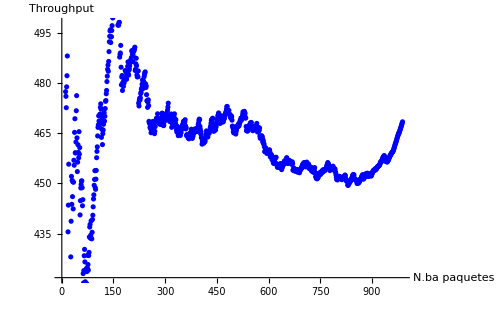
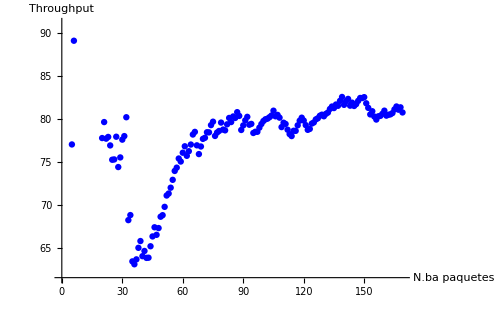
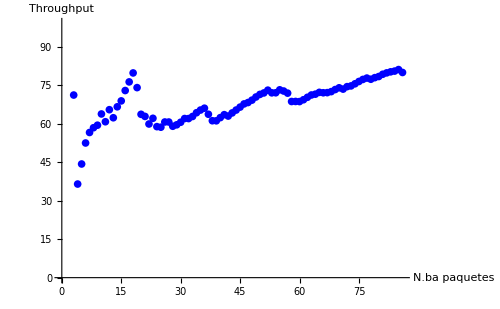
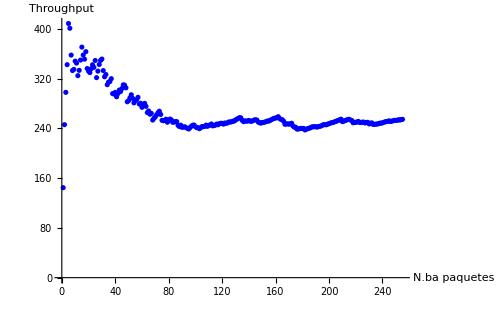
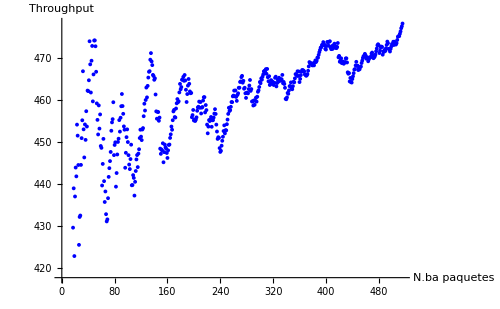
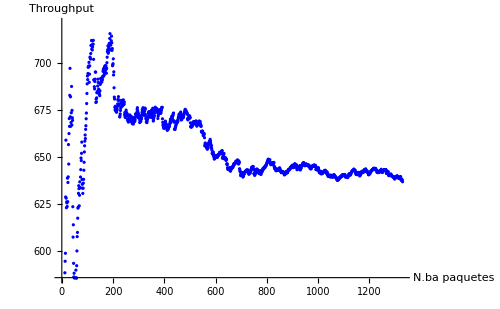
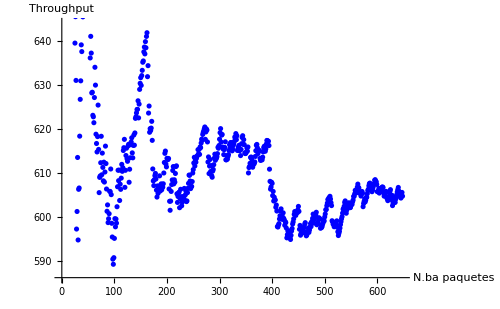
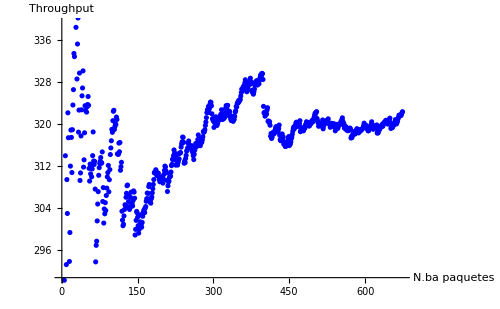
-Graphics-TH en ruta 1-2-3 | -Graphics-TH en ruta 1-5-2-3
-Graphics-TH en ruta 1-5-2-4 | -Graphics-TH en ruta 1-5-4
-Graphics-TH en ruta 1-2-4 | -Graphics-TH en ruta 2-3
-Graphics-TH en ruta 2-4 | -Graphics-TH en ruta 5-2-3
-Graphics-TH en ruta 5-2-4 | -Graphics-TH en ruta 5-4

```mathematica
(*Gráficas con ListPlot y etiquetas usando Labeled*)
grafica1=Labeled[ListPlot[ThroughputList[paquetes123],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 1-2-3"];
grafica2=Labeled[ListPlot[ThroughputList[paquetes1523],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 1-5-2-3"];
grafica3=Labeled[ListPlot[ThroughputList[paquetes1524],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 1-5-2-4"];
grafica4=Labeled[ListPlot[ThroughputList[paquetes154],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 1-5-4"];
grafica5=Labeled[ListPlot[ThroughputList[paquetes124],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 1-2-4"];
grafica6=Labeled[ListPlot[ThroughputList[paquetes23],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 2-3"];
grafica7=Labeled[ListPlot[ThroughputList[paquetes24],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 2-4"];
grafica8=Labeled[ListPlot[ThroughputList[paquetes523],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 5-2-3"];
grafica9=Labeled[ListPlot[ThroughputList[paquetes524],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 5-2-4"];
grafica10=Labeled[ListPlot[ThroughputList[paquetes54],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 5-4"];

(*Crear la tabla con 5 filas y 2 columnas*)
tablaListPlot10=Grid[{{grafica1,grafica2},{grafica3,grafica4},{grafica5,grafica6},{grafica7,grafica8},{grafica9,grafica10}},
ItemSize->{Automatic,Automatic},(*10 unidades de ancho para las celdas*)
Frame->All];

(*Mostrar la tabla*)
tablaListPlot10
```

```mathematica
ThroughputMax[paquetes123]
ThroughputMax[paquetes124]
ThroughputMax[paquetes1523]
ThroughputMax[paquetes1524]
ThroughputMax[paquetes154]
ThroughputMax[paquetes23]
ThroughputMax[paquetes24]
ThroughputMax[paquetes523]
ThroughputMax[paquetes524]
ThroughputMax[paquetes54] 
Last[paquetes123]
Last[paquetes123][[9]]
Length[paquetes123]
(Length[paquetes123]/Last[paquetes123][[1]])//N
```

468.43

478.303

80.766

80.0202

254.702

636.796

604.698

322.316

319.36

1002.44

{2.11131,526.898,3162,0,0,2012,1,{Ori-1,2,3},0.998918}

0.998918

989

468.43

# 7B.- Obtención de estadísticas y representación gráfica de resultados parciales CON protocolo S&W

```mathematica
(*Ejecución de la función*)
opcionesDistintas3SW=ObtenerOpcionesDistintas[out3SW]
opcionesDistintas4SW=ObtenerOpcionesDistintas[out4SW]

paquetes123SW = getPacketsWithRoute[out3SW,{"Ori-1",2,3}];
paquetes1523SW = getPacketsWithRoute[out3SW,{"Ori-1",5,2,3}];
paquetes1524SW = getPacketsWithRoute[out4SW,{"Ori-1",5,2,4}];
paquetes154SW = getPacketsWithRoute[out4SW,{"Ori-1",5,4}];
paquetes124SW = getPacketsWithRoute[out4SW,{"Ori-1",2,4}]; 
paquetes23SW= getPacketsWithRoute[out3SW,{"Ori-2",2,3}];
paquetes24SW = getPacketsWithRoute[out4SW,{"Ori-2",2,4}]; 
paquetes523SW = getPacketsWithRoute[out3SW,{"Ori-5",5,2,3}];
paquetes524SW = getPacketsWithRoute[out4SW,{"Ori-5",5,2,4}]; 
paquetes54SW = getPacketsWithRoute[out4SW,{"Ori-5",5,4}]; 

tot1SW = Length[out3SW]+Length[out4SW]
tot2SW = Length[paquetes123SW]+ Length[paquetes1523SW]+Length[paquetes154SW]+Length[paquetes1524SW]+ Length[paquetes124SW]+Length[paquetes23SW]+Length[paquetes24SW]+Length[paquetes523SW]+Length[paquetes524SW]+Length[paquetes54SW]
```

{{Ori-2,2,3},{Ori-5,5,2,3},{Ori-1,2,3},{Ori-1,5,2,3}}

{{Ori-5,5,2,4},{Ori-1,2,4},{Ori-1,5,4},{Ori-5,5,4},{Ori-2,2,4},{Ori-1,5,2,4}}

5904

5904

```mathematica
t123 = getRetardo[paquetes123SW]
t124= getRetardo[paquetes124SW]
t1523 = getRetardo[paquetes1523SW]
t1524 = getRetardo[paquetes1524SW]
t154 = getRetardo[paquetes154SW]
t23 = getRetardo[paquetes23SW]
t24 = getRetardo[paquetes24SW]
t523 = getRetardo[paquetes523SW]
t524 = getRetardo[paquetes524SW]
t54 = getRetardo[paquetes54SW]
```

0.228914

0.938017

0.132411

0.807836

0.0462012

0.116705

0.719977

0.143565

0.811857

0.0459131

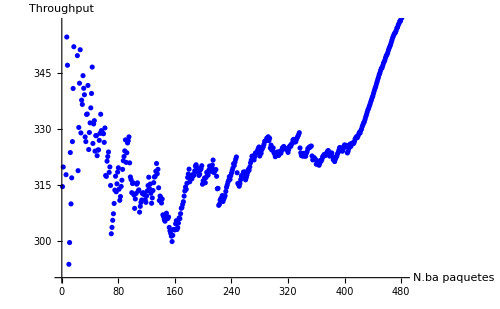
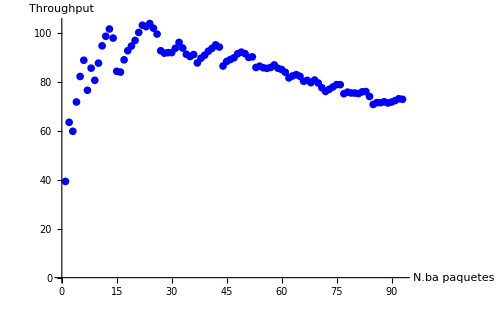
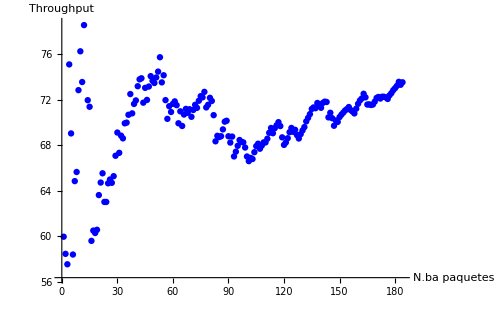
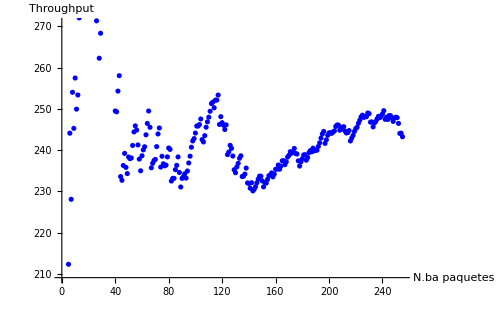
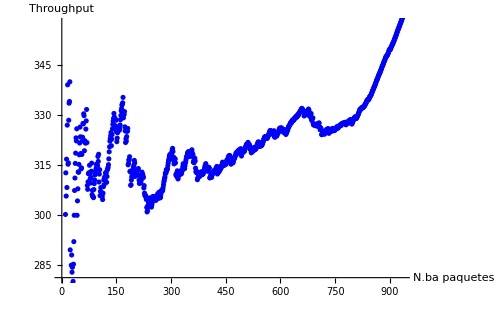
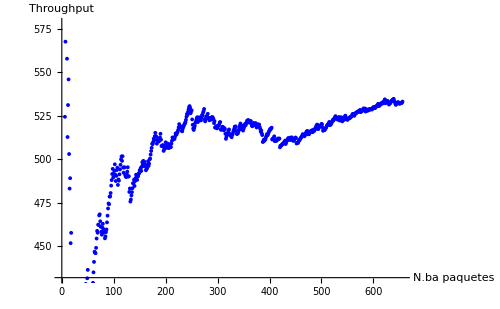
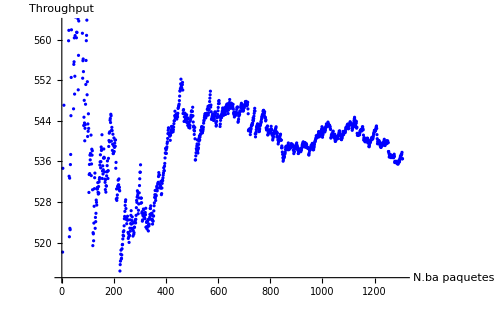
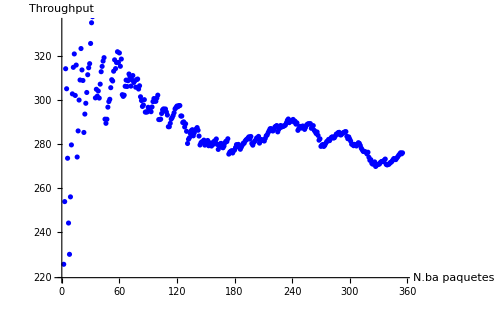
-Graphics-TH en ruta 1-2-3 | -Graphics-TH en ruta 1-5-2-3
-Graphics-TH en ruta 1-5-2-4 | -Graphics-TH en ruta 1-5-4
-Graphics-TH en ruta 1-2-4 | -Graphics-TH en ruta 2-3
-Graphics-TH en ruta 2-4 | -Graphics-TH en ruta 5-2-3
-Graphics-TH en ruta 5-2-4 | -Graphics-TH en ruta 5-4

```mathematica
(*Gráficas con ListPlot y etiquetas usando Labeled*)
grafica1=Labeled[ListPlot[ThroughputList[paquetes123SW],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 1-2-3"];
grafica2=Labeled[ListPlot[ThroughputList[paquetes1523SW],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 1-5-2-3"];
grafica3=Labeled[ListPlot[ThroughputList[paquetes1524SW],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 1-5-2-4"];
grafica4=Labeled[ListPlot[ThroughputList[paquetes154SW],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 1-5-4"];
grafica5=Labeled[ListPlot[ThroughputList[paquetes124SW],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 1-2-4"];
grafica6=Labeled[ListPlot[ThroughputList[paquetes23SW],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 2-3"];
grafica7=Labeled[ListPlot[ThroughputList[paquetes24SW],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 2-4"];
grafica8=Labeled[ListPlot[ThroughputList[paquetes523SW],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 5-2-3"];
grafica9=Labeled[ListPlot[ThroughputList[paquetes524SW],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 5-2-4"];
grafica10=Labeled[ListPlot[ThroughputList[paquetes54SW],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 5-4"];

(*Crear la tabla con 5 filas y 2 columnas*)
tablaListPlot10SW=Grid[{{grafica1,grafica2},{grafica3,grafica4},{grafica5,grafica6},{grafica7,grafica8},{grafica9,grafica10}},
ItemSize->{Automatic,Automatic},(*10 unidades de ancho para las celdas*)
Frame->All];

(*Mostrar la tabla*)
tablaListPlot10SW
```

```mathematica
ThroughputMax[paquetes123SW]
ThroughputMax[paquetes124SW]
ThroughputMax[paquetes1523SW]
ThroughputMax[paquetes1524SW]
ThroughputMax[paquetes154SW]
ThroughputMax[paquetes23SW]
ThroughputMax[paquetes24SW]
ThroughputMax[paquetes523SW]
ThroughputMax[paquetes524SW]
ThroughputMax[paquetes54SW]
```

360.312

359.265

72.9802

73.5389

243.233

533.092

536.548

276.048

260.255

931.024

# 7C.- Obtención de estadísticas y representación gráfica de resultados parciales CON protocolo GBN

```mathematica
(*Ejecución de la función*)
opcionesDistintas3GBN=ObtenerOpcionesDistintas[out3GBN]
opcionesDistintas4GBN=ObtenerOpcionesDistintas[out4GBN]

paquetes123GBN = getPacketsWithRoute[out3GBN,{"Ori-1",2,3}];
paquetes1523GBN = getPacketsWithRoute[out3GBN,{"Ori-1",5,2,3}];
paquetes1524GBN = getPacketsWithRoute[out4GBN,{"Ori-1",5,2,4}];
paquetes154GBN = getPacketsWithRoute[out4GBN,{"Ori-1",5,4}];
paquetes124GBN = getPacketsWithRoute[out4GBN,{"Ori-1",2,4}]; 
paquetes23GBN= getPacketsWithRoute[out3GBN,{"Ori-2",2,3}];
paquetes24GBN = getPacketsWithRoute[out4GBN,{"Ori-2",2,4}]; 
paquetes523GBN = getPacketsWithRoute[out3GBN,{"Ori-5",5,2,3}];
paquetes524GBN = getPacketsWithRoute[out4GBN,{"Ori-5",5,2,4}]; 
paquetes54GBN = getPacketsWithRoute[out4GBN,{"Ori-5",5,4}]; 

tot1GBN = Length[out3GBN]+Length[out4GBN]
tot2GBN = Length[paquetes123GBN]+ Length[paquetes1523GBN]+Length[paquetes154GBN]+Length[paquetes1524GBN]+ Length[paquetes124GBN]+Length[paquetes23GBN]+Length[paquetes24GBN]+Length[paquetes523GBN]+Length[paquetes524GBN]+Length[paquetes54GBN]
```

{{Ori-2,2,3},{Ori-5,5,2,3},{Ori-1,2,3},{Ori-1,5,2,3}}

{{Ori-5,5,4},{Ori-2,2,4},{Ori-1,5,4},{Ori-1,2,4},{Ori-1,5,2,4},{Ori-5,5,2,4}}

5937

5937

```mathematica
t123 = getRetardo[paquetes123GBN]
t124= getRetardo[paquetes124GBN]
t1523 = getRetardo[paquetes1523GBN]
t1524 = getRetardo[paquetes1524GBN]
t154 = getRetardo[paquetes154GBN]
t23 = getRetardo[paquetes23GBN]
t24 = getRetardo[paquetes24GBN]
t523 = getRetardo[paquetes523GBN]
t524 = getRetardo[paquetes524GBN]
t54 = getRetardo[paquetes54GBN]
```

0.193704

0.00315106

0.217008

0.00886159

0.00600101

0.197874

0.00275423

0.204887

0.00713324

0.00409745

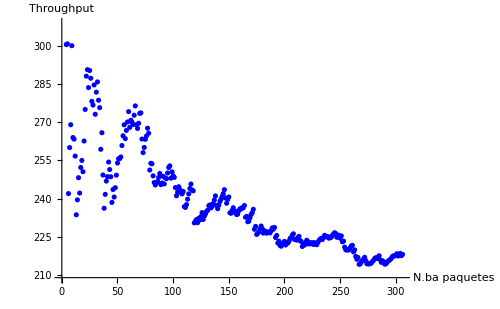
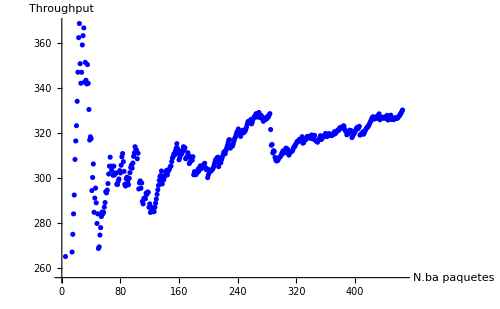
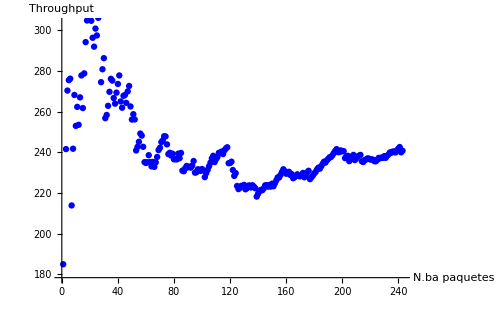
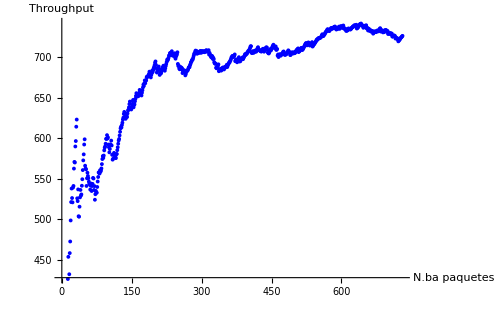
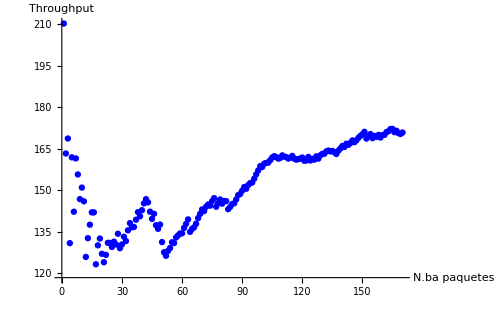
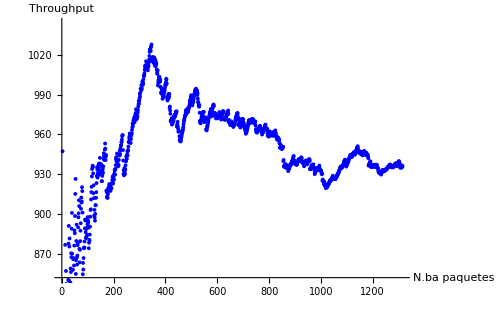
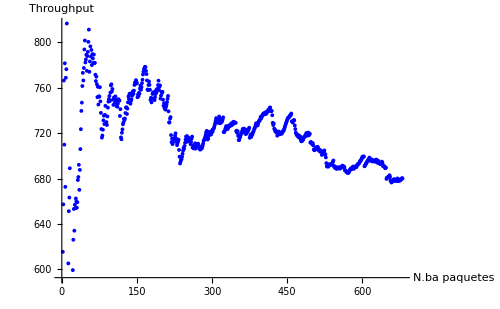
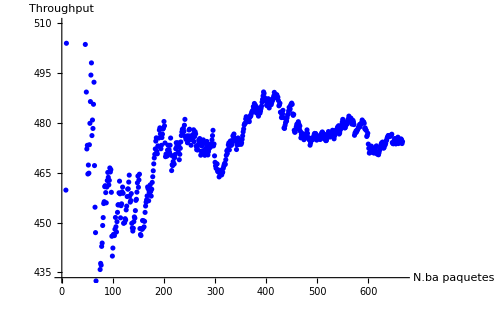
-Graphics-TH en ruta 1-2-3 | -Graphics-TH en ruta 1-5-2-3
-Graphics-TH en ruta 1-5-2-4 | -Graphics-TH en ruta 1-5-4
-Graphics-TH en ruta 1-2-4 | -Graphics-TH en ruta 2-3
-Graphics-TH en ruta 2-4 | -Graphics-TH en ruta 5-2-3
-Graphics-TH en ruta 5-2-4 | -Graphics-TH en ruta 5-4

```mathematica
(*Gráficas con ListPlot y etiquetas usando Labeled*)
grafica1=Labeled[ListPlot[ThroughputList[paquetes123GBN],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 1-2-3"];
grafica2=Labeled[ListPlot[ThroughputList[paquetes1523GBN],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 1-5-2-3"];
grafica3=Labeled[ListPlot[ThroughputList[paquetes1524GBN],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 1-5-2-4"];
grafica4=Labeled[ListPlot[ThroughputList[paquetes154GBN],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 1-5-4"];
grafica5=Labeled[ListPlot[ThroughputList[paquetes124GBN],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 1-2-4"];
grafica6=Labeled[ListPlot[ThroughputList[paquetes23GBN],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 2-3"];
grafica7=Labeled[ListPlot[ThroughputList[paquetes24GBN],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 2-4"];
grafica8=Labeled[ListPlot[ThroughputList[paquetes523GBN],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 5-2-3"];
grafica9=Labeled[ListPlot[ThroughputList[paquetes524GBN],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 5-2-4"];
grafica10=Labeled[ListPlot[ThroughputList[paquetes54GBN],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 5-4"];

(*Crear la tabla con 5 filas y 2 columnas*)
tablaListPlot10GBN=Grid[{{grafica1,grafica2},{grafica3,grafica4},{grafica5,grafica6},{grafica7,grafica8},{grafica9,grafica10}},
ItemSize->{Automatic,Automatic},(*10 unidades de ancho para las celdas*)
Frame->All];

(*Mostrar la tabla*)
tablaListPlot10GBN
```

```mathematica
ThroughputMax[paquetes123GBN]
ThroughputMax[paquetes124GBN]
ThroughputMax[paquetes1523GBN]
ThroughputMax[paquetes1524GBN]
ThroughputMax[paquetes154GBN]
ThroughputMax[paquetes23GBN]
ThroughputMax[paquetes24GBN]
ThroughputMax[paquetes523GBN]
ThroughputMax[paquetes524GBN]
ThroughputMax[paquetes54GBN]
```

218.161

170.862

330.261

240.762

726.107

935.724

680.108

474.391

333.916

1024.29